```mathematica
electron3Momentum[Ee_]:= √(Ee^2-mElectron^2);
mN = 1000;
mElectron = 0.5;
Q = 10;
neutrinoEnergy[Ee_,cosTheta_]:= √((electron3Momentum[Ee]*cosTheta+mN)^2-electron3Momentum[Ee]^2+2mN(Q+mElectron-Ee))-electron3Momentum[Ee]*cosTheta-mN;
fullyDifferential[Ee_,cosTheta_]:= 1+a*(electron3Momentum[Ee]*cosTheta)/Ee+b*mElectron/Ee;
```

```mathematica
Integrate[fullyDifferential[Ee,cosTheta],{Ee,mElectron,Q}]
```

9.2271 a cosTheta+1.49787 b+9.5

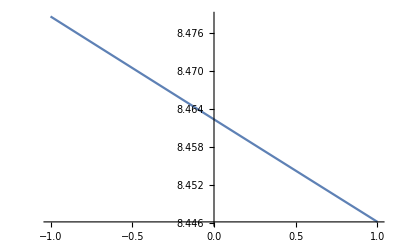

```mathematica
Plot[neutrinoEnergy[2,x],{x,-1,1}]
```

```mathematica
Reduce[{Sqrt[eElectron^2-mE^2]+eν Cos[θ]==pN Cos[θN],eν Sin[θ] == pN Sin[θN],Q == eElectron + eν + pN^2/(2mNeutron)-mE},{eElectron, θ,ΘN}]
```

Reduce::useq: The answer found by Reduce contains unsolved equation(s) {0==-mNeutron pN √(-20 mNeutron+2 eν mNeutron+pN^2) √(-20 mNeutron+2 eν mNeutron-4 mE mNeutron+pN^2)-√(mNeutron^2 pN^2 (Times[«2»]+Times[«3»]+Power[«2»]) (Times[«2»]+Times[«3»]+Times[«3»]+Power[«2»])),«9»,«20»}. A likely reason for this is that the solution set depends on branch cuts of Wolfram Language functions.

((θ-π)/(2 π)∉ℤ∧mNeutron≠0∧eν==0∧mE==-5∧pN==0∧eElectron==5)∨((θ-π)/(2 π)∉ℤ∧mNeutron≠0∧eν==0∧pN==-2 √5 √mNeutron∧cos(θN)==0∧sin(θN)==0∧eElectron==mE)∨((θ-π)/(2 π)∉ℤ∧mNeutron≠0∧eν==0∧pN==2 √5 √mNeutron∧cos(θN)==0∧sin(θN)==0∧eElectron==mE)∨(1∈ℤ∧0==-√(mNeutron^2 pN^2 (2 eν mNeutron-20 mNeutron+pN^2) (2 eν mNeutron-4 mE mNeutron-20 mNeutron+pN^2))-mNeutron pN √(2 eν mNeutron-20 mNeutron+pN^2) √(2 eν mNeutron-4 mE mNeutron-20 mNeutron+pN^2)∧mNeutron pN≠0∧0==1/(mNeutron^2 pN)(mNeutron^2 (-pN) √(((2 eν mNeutron-20 mNeutron+pN^2) (2 eν mNeutron-4 mE mNeutron-20 mNeutron+pN^2))/mNeutron^2)-√(mNeutron^2 pN^2 (2 eν mNeutron-20 mNeutron+pN^2) (2 eν mNeutron-4 mE mNeutron-20 mNeutron+pN^2)))∧cos(θN)==(√(((2 eν mNeutron-20 mNeutron+pN^2) (2 eν mNeutron-4 mE mNeutron-20 mNeutron+pN^2))/mNeutron^2)-2 eν)/(2 pN)∧sin(θN)==0∧eElectron==(-2 eν mNeutron+2 mE mNeutron+20 mNeutron-pN^2)/(2 mNeutron)∧θ==π+2 π 1)∨(1∈ℤ∧0==-√(mNeutron^2 pN^2 (2 eν mNeutron-20 mNeutron+pN^2) (2 eν mNeutron-4 mE mNeutron-20 mNeutron+pN^2))-mNeutron pN √(2 eν mNeutron-20 mNeutron+pN^2) √(2 eν mNeutron-4 mE mNeutron-20 mNeutron+pN^2)∧mNeutron pN≠0∧0==1/(mNeutron^2 pN)(√(mNeutron^2 pN^2 (2 eν mNeutron-20 mNeutron+pN^2) (2 eν mNeutron-4 mE mNeutron-20 mNeutron+pN^2))-mNeutron^2 pN √(((2 eν mNeutron-20 mNeutron+pN^2) (2 eν mNeutron-4 mE mNeutron-20 mNeutron+pN^2))/mNeutron^2))∧cos(θN)==(√(((2 eν mNeutron-20 mNeutron+pN^2) (2 eν mNeutron-4 mE mNeutron-20 mNeutron+pN^2))/mNeutron^2)-2 eν)/(2 pN)∧sin(θN)==0∧eElectron==(-2 eν mNeutron+2 mE mNeutron+20 mNeutron-pN^2)/(2 mNeutron)∧θ==π+2 π 1)∨(1∈ℤ∧0==mNeutron pN √(2 eν mNeutron-20 mNeutron+pN^2) √(2 eν mNeutron-4 mE mNeutron-20 mNeutron+pN^2)-√(mNeutron^2 pN^2 (2 eν mNeutron-20 mNeutron+pN^2) (2 eν mNeutron-4 mE mNeutron-20 mNeutron+pN^2))∧mNeutron pN≠0∧0==1/(mNeutron^2 pN)(mNeutron^2 (-pN) √(((2 eν mNeutron-20 mNeutron+pN^2) (2 eν mNeutron-4 mE mNeutron-20 mNeutron+pN^2))/mNeutron^2)-√(mNeutron^2 pN^2 (2 eν mNeutron-20 mNeutron+pN^2) (2 eν mNeutron-4 mE mNeutron-20 mNeutron+pN^2)))∧cos(θN)==(√(((2 eν mNeutron-20 mNeutron+pN^2) (2 eν mNeutron-4 mE mNeutron-20 mNeutron+pN^2))/mNeutron^2)-2 eν)/(2 pN)∧sin(θN)==0∧eElectron==(-2 eν mNeutron+2 mE mNeutron+20 mNeutron-pN^2)/(2 mNeutron)∧θ==π+2 π 1)∨(1∈ℤ∧0==mNeutron pN √(2 eν mNeutron-20 mNeutron+pN^2) √(2 eν mNeutron-4 mE mNeutron-20 mNeutron+pN^2)-√(mNeutron^2 pN^2 (2 eν mNeutron-20 mNeutron+pN^2) (2 eν mNeutron-4 mE mNeutron-20 mNeutron+pN^2))∧mNeutron pN≠0∧0==1/(mNeutron^2 pN)(√(mNeutron^2 pN^2 (2 eν mNeutron-20 mNeutron+pN^2) (2 eν mNeutron-4 mE mNeutron-20 mNeutron+pN^2))-mNeutron^2 pN √(((2 eν mNeutron-20 mNeutron+pN^2) (2 eν mNeutron-4 mE mNeutron-20 mNeutron+pN^2))/mNeutron^2))∧cos(θN)==(√(((2 eν mNeutron-20 mNeutron+pN^2) (2 eν mNeutron-4 mE mNeutron-20 mNeutron+pN^2))/mNeutron^2)-2 eν)/(2 pN)∧sin(θN)==0∧eElectron==(-2 eν mNeutron+2 mE mNeutron+20 mNeutron-pN^2)/(2 mNeutron)∧θ==π+2 π 1)∨(1∈ℤ∧mNeutron≠0∧0==eν-√(eν^2)∧eν-10≠0∧mE==-(10 (eν-5))/(eν-10)∧pN==0∧eElectron==(-eν^2+10 eν-50)/(eν-10)∧θ==π+2 π 1)∨(1∈ℤ∧mNeutron pN≠0∧8 eν mE mNeutron^2+80 eν mNeutron^2-4 eν mNeutron pN^2-80 mE mNeutron^2+4 mE mNeutron pN^2-400 mNeutron^2+40 mNeutron pN^2-pN^4≠0∧eν mNeutron (8 eν mE mNeutron^2+80 eν mNeutron^2-4 eν mNeutron pN^2-80 mE mNeutron^2+4 mE mNeutron pN^2-400 mNeutron^2+40 mNeutron pN^2-pN^4) (√(((2 eν mNeutron-20 mNeutron+pN^2) (2 eν mNeutron-4 mE mNeutron-20 mNeutron+pN^2))/mNeutron^2)+2 eν)≠0∧cos(θN)==0∧sin(θN)==-1/(2 mNeutron pN)ⅈ √(-8 eν mE mNeutron^2-80 eν mNeutron^2+4 eν mNeutron pN^2+80 mE mNeutron^2-4 mE mNeutron pN^2+400 mNeutron^2-40 mNeutron pN^2+pN^4)∧eElectron==(-2 eν mNeutron+2 mE mNeutron+20 mNeutron-pN^2)/(2 mNeutron)∧θ==2 π 1-2 ⅈ tanh^-1((mNeutron √(-8 eν mE mNeutron^2-80 eν mNeutron^2+4 eν mNeutron pN^2+80 mE mNeutron^2-4 mE mNeutron pN^2+400 mNeutron^2-40 mNeutron pN^2+pN^4) (√(((2 eν mNeutron-20 mNeutron+pN^2) (2 eν mNeutron-4 mE mNeutron-20 mNeutron+pN^2))/mNeutron^2)+2 eν))/(8 eν mE mNeutron^2+80 eν mNeutron^2-4 eν mNeutron pN^2-80 mE mNeutron^2+4 mE mNeutron pN^2-400 mNeutron^2+40 mNeutron pN^2-pN^4)))∨(1∈ℤ∧mNeutron pN≠0∧8 eν mE mNeutron^2+80 eν mNeutron^2-4 eν mNeutron pN^2-80 mE mNeutron^2+4 mE mNeutron pN^2-400 mNeutron^2+40 mNeutron pN^2-pN^4≠0∧eν mNeutron (8 eν mE mNeutron^2+80 eν mNeutron^2-4 eν mNeutron pN^2-80 mE mNeutron^2+4 mE mNeutron pN^2-400 mNeutron^2+40 mNeutron pN^2-pN^4) (√(((2 eν mNeutron-20 mNeutron+pN^2) (2 eν mNeutron-4 mE mNeutron-20 mNeutron+pN^2))/mNeutron^2)+2 eν)≠0∧cos(θN)==0∧sin(θN)==1/(2 mNeutron pN)ⅈ √(-8 eν mE mNeutron^2-80 eν mNeutron^2+4 eν mNeutron pN^2+80 mE mNeutron^2-4 mE mNeutron pN^2+400 mNeutron^2-40 mNeutron pN^2+pN^4)∧eElectron==(-2 eν mNeutron+2 mE mNeutron+20 mNeutron-pN^2)/(2 mNeutron)∧θ==2 ⅈ tanh^-1((mNeutron √(-8 eν mE mNeutron^2-80 eν mNeutron^2+4 eν mNeutron pN^2+80 mE mNeutron^2-4 mE mNeutron pN^2+400 mNeutron^2-40 mNeutron pN^2+pN^4) (√(((2 eν mNeutron-20 mNeutron+pN^2) (2 eν mNeutron-4 mE mNeutron-20 mNeutron+pN^2))/mNeutron^2)+2 eν))/(8 eν mE mNeutron^2+80 eν mNeutron^2-4 eν mNeutron pN^2-80 mE mNeutron^2+4 mE mNeutron pN^2-400 mNeutron^2+40 mNeutron pN^2-pN^4))+2 π 1)∨((θ-π)/(2 π)∉ℤ∧mNeutron≠0∧√((mE+5) mNeutron)≠0∧eν==0∧pN==-2 √((mE+5) mNeutron)∧cos(θN)==0∧sin(θN)==0∧eElectron==-mE)∨((θ-π)/(2 π)∉ℤ∧mNeutron≠0∧√((mE+5) mNeutron)≠0∧eν==0∧pN==2 √((mE+5) mNeutron)∧cos(θN)==0∧sin(θN)==0∧eElectron==-mE)∨((θ-π)/(2 π)∉ℤ∧mNeutron pN≠0∧0==1/(2 mNeutron)(mNeutron (-√(((20 mNeutron-pN^2) (4 mE mNeutron+20 mNeutron-pN^2))/mNeutron^2))-√(20 mNeutron-pN^2) √(4 mE mNeutron+20 mNeutron-pN^2))∧(mE+5) √(20 mNeutron-pN^2) √(4 mE mNeutron+20 mNeutron-pN^2)≠0∧eν==0∧cos(θN)==-(√(20 mNeutron-pN^2) √(4 mE mNeutron+20 mNeutron-pN^2))/(2 mNeutron pN)∧sin(θN)==0∧eElectron==(2 mE mNeutron+20 mNeutron-pN^2)/(2 mNeutron))∨((θ-π)/(2 π)∉ℤ∧mNeutron pN≠0∧0==1/(2 mNeutron)(√(20 mNeutron-pN^2) √(4 mE mNeutron+20 mNeutron-pN^2)-mNeutron √(((20 mNeutron-pN^2) (4 mE mNeutron+20 mNeutron-pN^2))/mNeutron^2))∧(mE+5) √(20 mNeutron-pN^2) √(4 mE mNeutron+20 mNeutron-pN^2)≠0∧eν==0∧cos(θN)==(√(20 mNeutron-pN^2) √(4 mE mNeutron+20 mNeutron-pN^2))/(2 mNeutron pN)∧sin(θN)==0∧eElectron==(2 mE mNeutron+20 mNeutron-pN^2)/(2 mNeutron))∨(1∈ℤ∧eν-10≠0∧0==-√(eν^2)-eν∧eν≠0∧mNeutron≠0∧mE==-(10 (eν-5))/(eν-10)∧pN==0∧eElectron==(-eν^2+10 eν-50)/(eν-10)∧θ==2 π 1)∨(1∈ℤ∧mNeutron pN≠0∧cos(θN)≠0∧0==1/(2 mNeutron^4 pN^3)sec(θN) (mNeutron^4 (-pN^3) cos(θN) √(-((2 eν mNeutron-20 mNeutron+pN^2) (-2 eν mNeutron+4 mE mNeutron+20 mNeutron-pN^2))/mNeutron^2)-√(-mNeutron^6 pN^6 cos^2(θN) (2 eν mNeutron-20 mNeutron+pN^2) (-2 eν mNeutron+4 mE mNeutron+20 mNeutron-pN^2)))∧(eν mE+10 eν-10 mE-50) √(1/(mNeutron^4 pN^4)(-4 √(mNeutron^6 pN^6 cos^2(θN) (2 eν mNeutron-20 mNeutron+pN^2) (2 eν mNeutron-4 mE mNeutron-20 mNeutron+pN^2))+8 eν mE mNeutron^4 pN^2+80 eν mNeutron^4 pN^2-4 eν mNeutron^3 pN^4-80 mE mNeutron^4 pN^2+4 mE mNeutron^3 pN^4-4 mNeutron^4 pN^4 cos^2(θN)-400 mNeutron^4 pN^2+40 mNeutron^3 pN^4-mNeutron^2 pN^6))≠0∧mNeutron^2 cos^2(θN) pN^12+mNeutron^4 cos^4(θN) pN^10+8 eν mNeutron^3 cos^2(θN) pN^10-8 mE mNeutron^3 cos^2(θN) pN^10-80 mNeutron^3 cos^2(θN) pN^10+4 eν mNeutron^4 cos^3(θN) pN^9+2 mNeutron^4 √(((pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron))/mNeutron^2) cos^3(θN) pN^9+4 eν mNeutron^5 cos^4(θN) pN^8-4 mE mNeutron^5 cos^4(θN) pN^8-40 mNeutron^5 cos^4(θN) pN^8+28 eν^2 mNeutron^4 cos^2(θN) pN^8+16 mE^2 mNeutron^4 cos^2(θN) pN^8-460 eν mNeutron^4 cos^2(θN) pN^8-46 eν mE mNeutron^4 cos^2(θN) pN^8+460 mE mNeutron^4 cos^2(θN) pN^8+2300 mNeutron^4 cos^2(θN) pN^8+4 eν mNeutron^4 √(((pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron))/mNeutron^2) cos^2(θN) pN^8+16 eν^2 mNeutron^5 cos^3(θN) pN^7-160 eν mNeutron^5 cos^3(θN) pN^7-16 eν mE mNeutron^5 cos^3(θN) pN^7+8 eν mNeutron^5 √(((pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron))/mNeutron^2) cos^3(θN) pN^7-8 mE mNeutron^5 √(((pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron))/mNeutron^2) cos^3(θN) pN^7-80 mNeutron^5 √(((pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron))/mNeutron^2) cos^3(θN) pN^7-80 eν^2 mNeutron^4 cos(θN) pN^7+400 eν mNeutron^4 cos(θN) pN^7-8 eν^2 mE mNeutron^4 cos(θN) pN^7+80 eν mE mNeutron^4 cos(θN) pN^7-20 eν mNeutron^4 √(((pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron))/mNeutron^2) cos(θN) pN^7-2 eν mE mNeutron^4 √(((pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron))/mNeutron^2) cos(θN) pN^7+20 mE mNeutron^4 √(((pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron))/mNeutron^2) cos(θN) pN^7+100 mNeutron^4 √(((pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron))/mNeutron^2) cos(θN) pN^7+4 eν^2 mNeutron^6 cos^4(θN) pN^6-80 eν mNeutron^6 cos^4(θN) pN^6-8 eν mE mNeutron^6 cos^4(θN) pN^6+80 mE mNeutron^6 cos^4(θN) pN^6+400 mNeutron^6 cos^4(θN) pN^6+48 eν^3 mNeutron^5 cos^2(θN) pN^6-1040 eν^2 mNeutron^5 cos^2(θN) pN^6+56 eν mE^2 mNeutron^5 cos^2(θN) pN^6-560 mE^2 mNeutron^5 cos^2(θN) pN^6+8400 eν mNeutron^5 cos^2(θN) pN^6-104 eν^2 mE mNeutron^5 cos^2(θN) pN^6+1680 eν mE mNeutron^5 cos^2(θN) pN^6-8400 mE mNeutron^5 cos^2(θN) pN^6-28000 mNeutron^5 cos^2(θN) pN^6+16 eν^2 mNeutron^5 √(((pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron))/mNeutron^2) cos^2(θN) pN^6-160 eν mNeutron^5 √(((pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron))/mNeutron^2) cos^2(θN) pN^6-16 eν mE mNeutron^5 √(((pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron))/mNeutron^2) cos^2(θN) pN^6+2 cos^2(θN) √(mNeutron^6 pN^6 (pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron) cos^2(θN)) pN^6+16 eν^3 mNeutron^6 cos^3(θN) pN^5-320 eν^2 mNeutron^6 cos^3(θN) pN^5+1600 eν mNeutron^6 cos^3(θN) pN^5-32 eν^2 mE mNeutron^6 cos^3(θN) pN^5+320 eν mE mNeutron^6 cos^3(θN) pN^5+8 eν^2 mNeutron^6 √(((pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron))/mNeutron^2) cos^3(θN) pN^5-120 eν mNeutron^6 √(((pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron))/mNeutron^2) cos^3(θN) pN^5-12 eν mE mNeutron^6 √(((pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron))/mNeutron^2) cos^3(θN) pN^5+120 mE mNeutron^6 √(((pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron))/mNeutron^2) cos^3(θN) pN^5+600 mNeutron^6 √(((pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron))/mNeutron^2) cos^3(θN) pN^5-320 eν^3 mNeutron^5 cos(θN) pN^5+4800 eν^2 mNeutron^5 cos(θN) pN^5+32 eν^2 mE^2 mNeutron^5 cos(θN) pN^5-320 eν mE^2 mNeutron^5 cos(θN) pN^5-16000 eν mNeutron^5 cos(θN) pN^5-32 eν^3 mE mNeutron^5 cos(θN) pN^5+960 eν^2 mE mNeutron^5 cos(θN) pN^5-4800 eν mE mNeutron^5 cos(θN) pN^5-80 eν^2 mNeutron^5 √(((pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron))/mNeutron^2) cos(θN) pN^5+8 eν mE^2 mNeutron^5 √(((pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron))/mNeutron^2) cos(θN) pN^5-80 mE^2 mNeutron^5 √(((pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron))/mNeutron^2) cos(θN) pN^5+1200 eν mNeutron^5 √(((pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron))/mNeutron^2) cos(θN) pN^5-8 eν^2 mE mNeutron^5 √(((pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron))/mNeutron^2) cos(θN) pN^5+240 eν mE mNeutron^5 √(((pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron))/mNeutron^2) cos(θN) pN^5-1200 mE mNeutron^5 √(((pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron))/mNeutron^2) cos(θN) pN^5-4000 mNeutron^5 √(((pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron))/mNeutron^2) cos(θN) pN^5+4 eν cos(θN) √(mNeutron^6 pN^6 (pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron) cos^2(θN)) pN^5+√(((pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron))/mNeutron^2) cos(θN) √(mNeutron^6 pN^6 (pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron) cos^2(θN)) pN^5+32 eν^4 mNeutron^6 cos^2(θN) pN^4-880 eν^3 mNeutron^6 cos^2(θN) pN^4+9200 eν^2 mNeutron^6 cos^2(θN) pN^4+48 eν^2 mE^2 mNeutron^6 cos^2(θN) pN^4-960 eν mE^2 mNeutron^6 cos^2(θN) pN^4+4800 mE^2 mNeutron^6 cos^2(θN) pN^4-48000 eν mNeutron^6 cos^2(θN) pN^4-88 eν^3 mE mNeutron^6 cos^2(θN) pN^4+1840 eν^2 mE mNeutron^6 cos^2(θN) pN^4-14400 eν mE mNeutron^6 cos^2(θN) pN^4+48000 mE mNeutron^6 cos^2(θN) pN^4+120000 mNeutron^6 cos^2(θN) pN^4+16 eν^3 mNeutron^6 √(((pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron))/mNeutron^2) cos^2(θN) pN^4-280 eν^2 mNeutron^6 √(((pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron))/mNeutron^2) cos^2(θN) pN^4+1400 eν mNeutron^6 √(((pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron))/mNeutron^2) cos^2(θN) pN^4-28 eν^2 mE mNeutron^6 √(((pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron))/mNeutron^2) cos^2(θN) pN^4+280 eν mE mNeutron^6 √(((pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron))/mNeutron^2) cos^2(θN) pN^4+8 eν mNeutron cos^2(θN) √(mNeutron^6 pN^6 (pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron) cos^2(θN)) pN^4-8 mE mNeutron cos^2(θN) √(mNeutron^6 pN^6 (pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron) cos^2(θN)) pN^4-80 mNeutron cos^2(θN) √(mNeutron^6 pN^6 (pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron) cos^2(θN)) pN^4-20 eν √(mNeutron^6 pN^6 (pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron) cos^2(θN)) pN^4-2 eν mE √(mNeutron^6 pN^6 (pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron) cos^2(θN)) pN^4+20 mE √(mNeutron^6 pN^6 (pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron) cos^2(θN)) pN^4+100 √(mNeutron^6 pN^6 (pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron) cos^2(θN)) pN^4-320 eν^4 mNeutron^6 cos(θN) pN^3+6400 eν^3 mNeutron^6 cos(θN) pN^3-48000 eν^2 mNeutron^6 cos(θN) pN^3+48 eν^3 mE^2 mNeutron^6 cos(θN) pN^3-960 eν^2 mE^2 mNeutron^6 cos(θN) pN^3+4800 eν mE^2 mNeutron^6 cos(θN) pN^3+120000 eν mNeutron^6 cos(θN) pN^3-32 eν^4 mE mNeutron^6 cos(θN) pN^3+1280 eν^3 mE mNeutron^6 cos(θN) pN^3-14400 eν^2 mE mNeutron^6 cos(θN) pN^3+48000 eν mE mNeutron^6 cos(θN) pN^3-160 eν^3 mNeutron^6 √(((pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron))/mNeutron^2) cos(θN) pN^3+1600 eν^2 mNeutron^6 √(((pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron))/mNeutron^2) cos(θN) pN^3+8 eν^2 mE^2 mNeutron^6 √(((pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron))/mNeutron^2) cos(θN) pN^3-160 eν mE^2 mNeutron^6 √(((pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron))/mNeutron^2) cos(θN) pN^3+800 mE^2 mNeutron^6 √(((pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron))/mNeutron^2) cos(θN) pN^3-8000 eν mNeutron^6 √(((pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron))/mNeutron^2) cos(θN) pN^3-16 eν^3 mE mNeutron^6 √(((pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron))/mNeutron^2) cos(θN) pN^3+320 eν^2 mE mNeutron^6 √(((pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron))/mNeutron^2) cos(θN) pN^3-2400 eν mE mNeutron^6 √(((pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron))/mNeutron^2) cos(θN) pN^3+8000 mE mNeutron^6 √(((pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron))/mNeutron^2) cos(θN) pN^3+20000 mNeutron^6 √(((pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron))/mNeutron^2) cos(θN) pN^3+mNeutron^2 √(((pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron))/mNeutron^2) cos^3(θN) √(mNeutron^6 pN^6 (pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron) cos^2(θN)) pN^3+16 eν^2 mNeutron cos(θN) √(mNeutron^6 pN^6 (pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron) cos^2(θN)) pN^3-160 eν mNeutron cos(θN) √(mNeutron^6 pN^6 (pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron) cos^2(θN)) pN^3-16 eν mE mNeutron cos(θN) √(mNeutron^6 pN^6 (pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron) cos^2(θN)) pN^3+4 eν mNeutron √(((pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron))/mNeutron^2) cos(θN) √(mNeutron^6 pN^6 (pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron) cos^2(θN)) pN^3-4 mE mNeutron √(((pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron))/mNeutron^2) cos(θN) √(mNeutron^6 pN^6 (pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron) cos^2(θN)) pN^3-40 mNeutron √(((pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron))/mNeutron^2) cos(θN) √(mNeutron^6 pN^6 (pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron) cos^2(θN)) pN^3+1600 eν^4 mNeutron^6 pN^2-16000 eν^3 mNeutron^6 pN^2+40000 eν^2 mNeutron^6 pN^2+16 eν^4 mE^2 mNeutron^6 pN^2-320 eν^3 mE^2 mNeutron^6 pN^2+1600 eν^2 mE^2 mNeutron^6 pN^2+320 eν^4 mE mNeutron^6 pN^2-4800 eν^3 mE mNeutron^6 pN^2+16000 eν^2 mE mNeutron^6 pN^2+800 eν^3 mNeutron^6 √(((pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron))/mNeutron^2) pN^2-8000 eν^2 mNeutron^6 √(((pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron))/mNeutron^2) pN^2+8 eν^3 mE^2 mNeutron^6 √(((pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron))/mNeutron^2) pN^2-160 eν^2 mE^2 mNeutron^6 √(((pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron))/mNeutron^2) pN^2+800 eν mE^2 mNeutron^6 √(((pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron))/mNeutron^2) pN^2+20000 eν mNeutron^6 √(((pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron))/mNeutron^2) pN^2+160 eν^3 mE mNeutron^6 √(((pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron))/mNeutron^2) pN^2-2400 eν^2 mE mNeutron^6 √(((pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron))/mNeutron^2) pN^2+8000 eν mE mNeutron^6 √(((pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron))/mNeutron^2) pN^2+8 eν^2 mNeutron^2 cos^2(θN) √(mNeutron^6 pN^6 (pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron) cos^2(θN)) pN^2-120 eν mNeutron^2 cos^2(θN) √(mNeutron^6 pN^6 (pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron) cos^2(θN)) pN^2-12 eν mE mNeutron^2 cos^2(θN) √(mNeutron^6 pN^6 (pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron) cos^2(θN)) pN^2+120 mE mNeutron^2 cos^2(θN) √(mNeutron^6 pN^6 (pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron) cos^2(θN)) pN^2+600 mNeutron^2 cos^2(θN) √(mNeutron^6 pN^6 (pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron) cos^2(θN)) pN^2+4 eν mNeutron^2 √(((pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron))/mNeutron^2) cos^2(θN) √(mNeutron^6 pN^6 (pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron) cos^2(θN)) pN^2-80 eν^2 mNeutron √(mNeutron^6 pN^6 (pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron) cos^2(θN)) pN^2+8 eν mE^2 mNeutron √(mNeutron^6 pN^6 (pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron) cos^2(θN)) pN^2-80 mE^2 mNeutron √(mNeutron^6 pN^6 (pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron) cos^2(θN)) pN^2+1200 eν mNeutron √(mNeutron^6 pN^6 (pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron) cos^2(θN)) pN^2-8 eν^2 mE mNeutron √(mNeutron^6 pN^6 (pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron) cos^2(θN)) pN^2+240 eν mE mNeutron √(mNeutron^6 pN^6 (pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron) cos^2(θN)) pN^2-1200 mE mNeutron √(mNeutron^6 pN^6 (pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron) cos^2(θN)) pN^2-4000 mNeutron √(mNeutron^6 pN^6 (pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron) cos^2(θN)) pN^2+16 eν^3 mNeutron^2 cos(θN) √(mNeutron^6 pN^6 (pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron) cos^2(θN)) pN-280 eν^2 mNeutron^2 cos(θN) √(mNeutron^6 pN^6 (pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron) cos^2(θN)) pN+1400 eν mNeutron^2 cos(θN) √(mNeutron^6 pN^6 (pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron) cos^2(θN)) pN-28 eν^2 mE mNeutron^2 cos(θN) √(mNeutron^6 pN^6 (pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron) cos^2(θN)) pN+280 eν mE mNeutron^2 cos(θN) √(mNeutron^6 pN^6 (pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron) cos^2(θN)) pN+8 eν^2 mNeutron^2 √(((pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron))/mNeutron^2) cos(θN) √(mNeutron^6 pN^6 (pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron) cos^2(θN)) pN-60 eν mNeutron^2 √(((pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron))/mNeutron^2) cos(θN) √(mNeutron^6 pN^6 (pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron) cos^2(θN)) pN-6 eν mE mNeutron^2 √(((pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron))/mNeutron^2) cos(θN) √(mNeutron^6 pN^6 (pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron) cos^2(θN)) pN+60 mE mNeutron^2 √(((pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron))/mNeutron^2) cos(θN) √(mNeutron^6 pN^6 (pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron) cos^2(θN)) pN+300 mNeutron^2 √(((pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron))/mNeutron^2) cos(θN) √(mNeutron^6 pN^6 (pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron) cos^2(θN)) pN-160 eν^3 mNeutron^2 √(mNeutron^6 pN^6 (pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron) cos^2(θN))+1600 eν^2 mNeutron^2 √(mNeutron^6 pN^6 (pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron) cos^2(θN))+8 eν^2 mE^2 mNeutron^2 √(mNeutron^6 pN^6 (pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron) cos^2(θN))-160 eν mE^2 mNeutron^2 √(mNeutron^6 pN^6 (pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron) cos^2(θN))+800 mE^2 mNeutron^2 √(mNeutron^6 pN^6 (pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron) cos^2(θN))-8000 eν mNeutron^2 √(mNeutron^6 pN^6 (pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron) cos^2(θN))-16 eν^3 mE mNeutron^2 √(mNeutron^6 pN^6 (pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron) cos^2(θN))+320 eν^2 mE mNeutron^2 √(mNeutron^6 pN^6 (pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron) cos^2(θN))-2400 eν mE mNeutron^2 √(mNeutron^6 pN^6 (pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron) cos^2(θN))+8000 mE mNeutron^2 √(mNeutron^6 pN^6 (pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron) cos^2(θN))+20000 mNeutron^2 √(mNeutron^6 pN^6 (pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron) cos^2(θN))-80 eν^2 mNeutron^2 √(((pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron))/mNeutron^2) √(mNeutron^6 pN^6 (pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron) cos^2(θN))+400 eν mNeutron^2 √(((pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron))/mNeutron^2) √(mNeutron^6 pN^6 (pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron) cos^2(θN))-8 eν^2 mE mNeutron^2 √(((pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron))/mNeutron^2) √(mNeutron^6 pN^6 (pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron) cos^2(θN))+80 eν mE mNeutron^2 √(((pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron))/mNeutron^2) √(mNeutron^6 pN^6 (pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron) cos^2(θN))≠0∧sin(θN)==-1/2 √(1/(mNeutron^4 pN^4)(-4 √(mNeutron^6 pN^6 cos^2(θN) (2 eν mNeutron-20 mNeutron+pN^2) (2 eν mNeutron-4 mE mNeutron-20 mNeutron+pN^2))+8 eν mE mNeutron^4 pN^2+80 eν mNeutron^4 pN^2-4 eν mNeutron^3 pN^4-80 mE mNeutron^4 pN^2+4 mE mNeutron^3 pN^4-4 mNeutron^4 pN^4 cos^2(θN)-400 mNeutron^4 pN^2+40 mNeutron^3 pN^4-mNeutron^2 pN^6))∧eElectron==(-2 eν mNeutron+2 mE mNeutron+20 mNeutron-pN^2)/(2 mNeutron)∧θ==2 tan^-1((-4 eν^2 mE mNeutron^4 pN^2+4 eν^2 mNeutron^4 pN^3 cos(θN)-40 eν^2 mNeutron^4 pN^2+pN cos(θN) √(mNeutron^6 pN^6 cos^2(θN) (2 eν mNeutron-20 mNeutron+pN^2) (2 eν mNeutron-4 mE mNeutron-20 mNeutron+pN^2))+2 eν √(mNeutron^6 pN^6 cos^2(θN) (2 eν mNeutron-20 mNeutron+pN^2) (2 eν mNeutron-4 mE mNeutron-20 mNeutron+pN^2))-4 eν mE mNeutron^4 pN^3 cos(θN)+40 eν mE mNeutron^4 pN^2+√(((2 eν mNeutron-20 mNeutron+pN^2) (2 eν mNeutron-4 mE mNeutron-20 mNeutron+pN^2))/mNeutron^2) √(mNeutron^6 pN^6 cos^2(θN) (2 eν mNeutron-20 mNeutron+pN^2) (2 eν mNeutron-4 mE mNeutron-20 mNeutron+pN^2))-20 eν mNeutron^4 pN^2 √(((2 eν mNeutron-20 mNeutron+pN^2) (2 eν mNeutron-4 mE mNeutron-20 mNeutron+pN^2))/mNeutron^2)-2 eν mE mNeutron^4 pN^2 √(((2 eν mNeutron-20 mNeutron+pN^2) (2 eν mNeutron-4 mE mNeutron-20 mNeutron+pN^2))/mNeutron^2)+20 mE mNeutron^4 pN^2 √(((2 eν mNeutron-20 mNeutron+pN^2) (2 eν mNeutron-4 mE mNeutron-20 mNeutron+pN^2))/mNeutron^2)+100 mNeutron^4 pN^2 √(((2 eν mNeutron-20 mNeutron+pN^2) (2 eν mNeutron-4 mE mNeutron-20 mNeutron+pN^2))/mNeutron^2)+mNeutron^4 pN^4 cos^2(θN) √(((2 eν mNeutron-20 mNeutron+pN^2) (2 eν mNeutron-4 mE mNeutron-20 mNeutron+pN^2))/mNeutron^2)+2 eν mNeutron^4 pN^3 cos(θN) √(((2 eν mNeutron-20 mNeutron+pN^2) (2 eν mNeutron-4 mE mNeutron-20 mNeutron+pN^2))/mNeutron^2)-40 eν mNeutron^4 pN^3 cos(θN)+200 eν mNeutron^4 pN^2+4 eν mNeutron^3 pN^5 cos(θN)+40 mE mNeutron^4 pN^3 cos(θN)-4 mE mNeutron^3 pN^5 cos(θN)+200 mNeutron^4 pN^3 cos(θN)-40 mNeutron^3 pN^5 cos(θN)+mNeutron^2 pN^7 cos(θN))/(2 mNeutron^4 pN^3 (eν mE+10 eν-10 mE-50) √(1/(mNeutron^4 pN^4)(-4 √(mNeutron^6 pN^6 cos^2(θN) (2 eν mNeutron-20 mNeutron+pN^2) (2 eν mNeutron-4 mE mNeutron-20 mNeutron+pN^2))+8 eν mE mNeutron^4 pN^2+80 eν mNeutron^4 pN^2-4 eν mNeutron^3 pN^4-80 mE mNeutron^4 pN^2+4 mE mNeutron^3 pN^4-4 mNeutron^4 pN^4 cos^2(θN)-400 mNeutron^4 pN^2+40 mNeutron^3 pN^4-mNeutron^2 pN^6))))+2 π 1)∨(1∈ℤ∧mNeutron pN≠0∧cos(θN)≠0∧0==1/(2 mNeutron^4 pN^3)sec(θN) (mNeutron^4 (-pN^3) cos(θN) √(-((2 eν mNeutron-20 mNeutron+pN^2) (-2 eν mNeutron+4 mE mNeutron+20 mNeutron-pN^2))/mNeutron^2)-√(-mNeutron^6 pN^6 cos^2(θN) (2 eν mNeutron-20 mNeutron+pN^2) (-2 eν mNeutron+4 mE mNeutron+20 mNeutron-pN^2)))∧(eν mE+10 eν-10 mE-50) √(1/(mNeutron^4 pN^4)(-4 √(mNeutron^6 pN^6 cos^2(θN) (2 eν mNeutron-20 mNeutron+pN^2) (2 eν mNeutron-4 mE mNeutron-20 mNeutron+pN^2))+8 eν mE mNeutron^4 pN^2+80 eν mNeutron^4 pN^2-4 eν mNeutron^3 pN^4-80 mE mNeutron^4 pN^2+4 mE mNeutron^3 pN^4-4 mNeutron^4 pN^4 cos^2(θN)-400 mNeutron^4 pN^2+40 mNeutron^3 pN^4-mNeutron^2 pN^6))≠0∧mNeutron^2 cos^2(θN) pN^12+mNeutron^4 cos^4(θN) pN^10+8 eν mNeutron^3 cos^2(θN) pN^10-8 mE mNeutron^3 cos^2(θN) pN^10-80 mNeutron^3 cos^2(θN) pN^10+4 eν mNeutron^4 cos^3(θN) pN^9+2 mNeutron^4 √(((pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron))/mNeutron^2) cos^3(θN) pN^9+4 eν mNeutron^5 cos^4(θN) pN^8-4 mE mNeutron^5 cos^4(θN) pN^8-40 mNeutron^5 cos^4(θN) pN^8+28 eν^2 mNeutron^4 cos^2(θN) pN^8+16 mE^2 mNeutron^4 cos^2(θN) pN^8-460 eν mNeutron^4 cos^2(θN) pN^8-46 eν mE mNeutron^4 cos^2(θN) pN^8+460 mE mNeutron^4 cos^2(θN) pN^8+2300 mNeutron^4 cos^2(θN) pN^8+4 eν mNeutron^4 √(((pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron))/mNeutron^2) cos^2(θN) pN^8+16 eν^2 mNeutron^5 cos^3(θN) pN^7-160 eν mNeutron^5 cos^3(θN) pN^7-16 eν mE mNeutron^5 cos^3(θN) pN^7+8 eν mNeutron^5 √(((pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron))/mNeutron^2) cos^3(θN) pN^7-8 mE mNeutron^5 √(((pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron))/mNeutron^2) cos^3(θN) pN^7-80 mNeutron^5 √(((pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron))/mNeutron^2) cos^3(θN) pN^7-80 eν^2 mNeutron^4 cos(θN) pN^7+400 eν mNeutron^4 cos(θN) pN^7-8 eν^2 mE mNeutron^4 cos(θN) pN^7+80 eν mE mNeutron^4 cos(θN) pN^7-20 eν mNeutron^4 √(((pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron))/mNeutron^2) cos(θN) pN^7-2 eν mE mNeutron^4 √(((pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron))/mNeutron^2) cos(θN) pN^7+20 mE mNeutron^4 √(((pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron))/mNeutron^2) cos(θN) pN^7+100 mNeutron^4 √(((pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron))/mNeutron^2) cos(θN) pN^7+4 eν^2 mNeutron^6 cos^4(θN) pN^6-80 eν mNeutron^6 cos^4(θN) pN^6-8 eν mE mNeutron^6 cos^4(θN) pN^6+80 mE mNeutron^6 cos^4(θN) pN^6+400 mNeutron^6 cos^4(θN) pN^6+48 eν^3 mNeutron^5 cos^2(θN) pN^6-1040 eν^2 mNeutron^5 cos^2(θN) pN^6+56 eν mE^2 mNeutron^5 cos^2(θN) pN^6-560 mE^2 mNeutron^5 cos^2(θN) pN^6+8400 eν mNeutron^5 cos^2(θN) pN^6-104 eν^2 mE mNeutron^5 cos^2(θN) pN^6+1680 eν mE mNeutron^5 cos^2(θN) pN^6-8400 mE mNeutron^5 cos^2(θN) pN^6-28000 mNeutron^5 cos^2(θN) pN^6+16 eν^2 mNeutron^5 √(((pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron))/mNeutron^2) cos^2(θN) pN^6-160 eν mNeutron^5 √(((pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron))/mNeutron^2) cos^2(θN) pN^6-16 eν mE mNeutron^5 √(((pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron))/mNeutron^2) cos^2(θN) pN^6+2 cos^2(θN) √(mNeutron^6 pN^6 (pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron) cos^2(θN)) pN^6+16 eν^3 mNeutron^6 cos^3(θN) pN^5-320 eν^2 mNeutron^6 cos^3(θN) pN^5+1600 eν mNeutron^6 cos^3(θN) pN^5-32 eν^2 mE mNeutron^6 cos^3(θN) pN^5+320 eν mE mNeutron^6 cos^3(θN) pN^5+8 eν^2 mNeutron^6 √(((pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron))/mNeutron^2) cos^3(θN) pN^5-120 eν mNeutron^6 √(((pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron))/mNeutron^2) cos^3(θN) pN^5-12 eν mE mNeutron^6 √(((pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron))/mNeutron^2) cos^3(θN) pN^5+120 mE mNeutron^6 √(((pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron))/mNeutron^2) cos^3(θN) pN^5+600 mNeutron^6 √(((pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron))/mNeutron^2) cos^3(θN) pN^5-320 eν^3 mNeutron^5 cos(θN) pN^5+4800 eν^2 mNeutron^5 cos(θN) pN^5+32 eν^2 mE^2 mNeutron^5 cos(θN) pN^5-320 eν mE^2 mNeutron^5 cos(θN) pN^5-16000 eν mNeutron^5 cos(θN) pN^5-32 eν^3 mE mNeutron^5 cos(θN) pN^5+960 eν^2 mE mNeutron^5 cos(θN) pN^5-4800 eν mE mNeutron^5 cos(θN) pN^5-80 eν^2 mNeutron^5 √(((pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron))/mNeutron^2) cos(θN) pN^5+8 eν mE^2 mNeutron^5 √(((pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron))/mNeutron^2) cos(θN) pN^5-80 mE^2 mNeutron^5 √(((pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron))/mNeutron^2) cos(θN) pN^5+1200 eν mNeutron^5 √(((pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron))/mNeutron^2) cos(θN) pN^5-8 eν^2 mE mNeutron^5 √(((pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron))/mNeutron^2) cos(θN) pN^5+240 eν mE mNeutron^5 √(((pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron))/mNeutron^2) cos(θN) pN^5-1200 mE mNeutron^5 √(((pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron))/mNeutron^2) cos(θN) pN^5-4000 mNeutron^5 √(((pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron))/mNeutron^2) cos(θN) pN^5+4 eν cos(θN) √(mNeutron^6 pN^6 (pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron) cos^2(θN)) pN^5+√(((pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron))/mNeutron^2) cos(θN) √(mNeutron^6 pN^6 (pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron) cos^2(θN)) pN^5+32 eν^4 mNeutron^6 cos^2(θN) pN^4-880 eν^3 mNeutron^6 cos^2(θN) pN^4+9200 eν^2 mNeutron^6 cos^2(θN) pN^4+48 eν^2 mE^2 mNeutron^6 cos^2(θN) pN^4-960 eν mE^2 mNeutron^6 cos^2(θN) pN^4+4800 mE^2 mNeutron^6 cos^2(θN) pN^4-48000 eν mNeutron^6 cos^2(θN) pN^4-88 eν^3 mE mNeutron^6 cos^2(θN) pN^4+1840 eν^2 mE mNeutron^6 cos^2(θN) pN^4-14400 eν mE mNeutron^6 cos^2(θN) pN^4+48000 mE mNeutron^6 cos^2(θN) pN^4+120000 mNeutron^6 cos^2(θN) pN^4+16 eν^3 mNeutron^6 √(((pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron))/mNeutron^2) cos^2(θN) pN^4-280 eν^2 mNeutron^6 √(((pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron))/mNeutron^2) cos^2(θN) pN^4+1400 eν mNeutron^6 √(((pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron))/mNeutron^2) cos^2(θN) pN^4-28 eν^2 mE mNeutron^6 √(((pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron))/mNeutron^2) cos^2(θN) pN^4+280 eν mE mNeutron^6 √(((pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron))/mNeutron^2) cos^2(θN) pN^4+8 eν mNeutron cos^2(θN) √(mNeutron^6 pN^6 (pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron) cos^2(θN)) pN^4-8 mE mNeutron cos^2(θN) √(mNeutron^6 pN^6 (pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron) cos^2(θN)) pN^4-80 mNeutron cos^2(θN) √(mNeutron^6 pN^6 (pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron) cos^2(θN)) pN^4-20 eν √(mNeutron^6 pN^6 (pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron) cos^2(θN)) pN^4-2 eν mE √(mNeutron^6 pN^6 (pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron) cos^2(θN)) pN^4+20 mE √(mNeutron^6 pN^6 (pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron) cos^2(θN)) pN^4+100 √(mNeutron^6 pN^6 (pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron) cos^2(θN)) pN^4-320 eν^4 mNeutron^6 cos(θN) pN^3+6400 eν^3 mNeutron^6 cos(θN) pN^3-48000 eν^2 mNeutron^6 cos(θN) pN^3+48 eν^3 mE^2 mNeutron^6 cos(θN) pN^3-960 eν^2 mE^2 mNeutron^6 cos(θN) pN^3+4800 eν mE^2 mNeutron^6 cos(θN) pN^3+120000 eν mNeutron^6 cos(θN) pN^3-32 eν^4 mE mNeutron^6 cos(θN) pN^3+1280 eν^3 mE mNeutron^6 cos(θN) pN^3-14400 eν^2 mE mNeutron^6 cos(θN) pN^3+48000 eν mE mNeutron^6 cos(θN) pN^3-160 eν^3 mNeutron^6 √(((pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron))/mNeutron^2) cos(θN) pN^3+1600 eν^2 mNeutron^6 √(((pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron))/mNeutron^2) cos(θN) pN^3+8 eν^2 mE^2 mNeutron^6 √(((pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron))/mNeutron^2) cos(θN) pN^3-160 eν mE^2 mNeutron^6 √(((pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron))/mNeutron^2) cos(θN) pN^3+800 mE^2 mNeutron^6 √(((pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron))/mNeutron^2) cos(θN) pN^3-8000 eν mNeutron^6 √(((pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron))/mNeutron^2) cos(θN) pN^3-16 eν^3 mE mNeutron^6 √(((pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron))/mNeutron^2) cos(θN) pN^3+320 eν^2 mE mNeutron^6 √(((pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron))/mNeutron^2) cos(θN) pN^3-2400 eν mE mNeutron^6 √(((pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron))/mNeutron^2) cos(θN) pN^3+8000 mE mNeutron^6 √(((pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron))/mNeutron^2) cos(θN) pN^3+20000 mNeutron^6 √(((pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron))/mNeutron^2) cos(θN) pN^3+mNeutron^2 √(((pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron))/mNeutron^2) cos^3(θN) √(mNeutron^6 pN^6 (pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron) cos^2(θN)) pN^3+16 eν^2 mNeutron cos(θN) √(mNeutron^6 pN^6 (pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron) cos^2(θN)) pN^3-160 eν mNeutron cos(θN) √(mNeutron^6 pN^6 (pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron) cos^2(θN)) pN^3-16 eν mE mNeutron cos(θN) √(mNeutron^6 pN^6 (pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron) cos^2(θN)) pN^3+4 eν mNeutron √(((pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron))/mNeutron^2) cos(θN) √(mNeutron^6 pN^6 (pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron) cos^2(θN)) pN^3-4 mE mNeutron √(((pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron))/mNeutron^2) cos(θN) √(mNeutron^6 pN^6 (pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron) cos^2(θN)) pN^3-40 mNeutron √(((pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron))/mNeutron^2) cos(θN) √(mNeutron^6 pN^6 (pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron) cos^2(θN)) pN^3+1600 eν^4 mNeutron^6 pN^2-16000 eν^3 mNeutron^6 pN^2+40000 eν^2 mNeutron^6 pN^2+16 eν^4 mE^2 mNeutron^6 pN^2-320 eν^3 mE^2 mNeutron^6 pN^2+1600 eν^2 mE^2 mNeutron^6 pN^2+320 eν^4 mE mNeutron^6 pN^2-4800 eν^3 mE mNeutron^6 pN^2+16000 eν^2 mE mNeutron^6 pN^2+800 eν^3 mNeutron^6 √(((pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron))/mNeutron^2) pN^2-8000 eν^2 mNeutron^6 √(((pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron))/mNeutron^2) pN^2+8 eν^3 mE^2 mNeutron^6 √(((pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron))/mNeutron^2) pN^2-160 eν^2 mE^2 mNeutron^6 √(((pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron))/mNeutron^2) pN^2+800 eν mE^2 mNeutron^6 √(((pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron))/mNeutron^2) pN^2+20000 eν mNeutron^6 √(((pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron))/mNeutron^2) pN^2+160 eν^3 mE mNeutron^6 √(((pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron))/mNeutron^2) pN^2-2400 eν^2 mE mNeutron^6 √(((pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron))/mNeutron^2) pN^2+8000 eν mE mNeutron^6 √(((pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron))/mNeutron^2) pN^2+8 eν^2 mNeutron^2 cos^2(θN) √(mNeutron^6 pN^6 (pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron) cos^2(θN)) pN^2-120 eν mNeutron^2 cos^2(θN) √(mNeutron^6 pN^6 (pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron) cos^2(θN)) pN^2-12 eν mE mNeutron^2 cos^2(θN) √(mNeutron^6 pN^6 (pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron) cos^2(θN)) pN^2+120 mE mNeutron^2 cos^2(θN) √(mNeutron^6 pN^6 (pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron) cos^2(θN)) pN^2+600 mNeutron^2 cos^2(θN) √(mNeutron^6 pN^6 (pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron) cos^2(θN)) pN^2+4 eν mNeutron^2 √(((pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron))/mNeutron^2) cos^2(θN) √(mNeutron^6 pN^6 (pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron) cos^2(θN)) pN^2-80 eν^2 mNeutron √(mNeutron^6 pN^6 (pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron) cos^2(θN)) pN^2+8 eν mE^2 mNeutron √(mNeutron^6 pN^6 (pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron) cos^2(θN)) pN^2-80 mE^2 mNeutron √(mNeutron^6 pN^6 (pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron) cos^2(θN)) pN^2+1200 eν mNeutron √(mNeutron^6 pN^6 (pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron) cos^2(θN)) pN^2-8 eν^2 mE mNeutron √(mNeutron^6 pN^6 (pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron) cos^2(θN)) pN^2+240 eν mE mNeutron √(mNeutron^6 pN^6 (pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron) cos^2(θN)) pN^2-1200 mE mNeutron √(mNeutron^6 pN^6 (pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron) cos^2(θN)) pN^2-4000 mNeutron √(mNeutron^6 pN^6 (pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron) cos^2(θN)) pN^2+16 eν^3 mNeutron^2 cos(θN) √(mNeutron^6 pN^6 (pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron) cos^2(θN)) pN-280 eν^2 mNeutron^2 cos(θN) √(mNeutron^6 pN^6 (pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron) cos^2(θN)) pN+1400 eν mNeutron^2 cos(θN) √(mNeutron^6 pN^6 (pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron) cos^2(θN)) pN-28 eν^2 mE mNeutron^2 cos(θN) √(mNeutron^6 pN^6 (pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron) cos^2(θN)) pN+280 eν mE mNeutron^2 cos(θN) √(mNeutron^6 pN^6 (pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron) cos^2(θN)) pN+8 eν^2 mNeutron^2 √(((pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron))/mNeutron^2) cos(θN) √(mNeutron^6 pN^6 (pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron) cos^2(θN)) pN-60 eν mNeutron^2 √(((pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron))/mNeutron^2) cos(θN) √(mNeutron^6 pN^6 (pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron) cos^2(θN)) pN-6 eν mE mNeutron^2 √(((pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron))/mNeutron^2) cos(θN) √(mNeutron^6 pN^6 (pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron) cos^2(θN)) pN+60 mE mNeutron^2 √(((pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron))/mNeutron^2) cos(θN) √(mNeutron^6 pN^6 (pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron) cos^2(θN)) pN+300 mNeutron^2 √(((pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron))/mNeutron^2) cos(θN) √(mNeutron^6 pN^6 (pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron) cos^2(θN)) pN-160 eν^3 mNeutron^2 √(mNeutron^6 pN^6 (pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron) cos^2(θN))+1600 eν^2 mNeutron^2 √(mNeutron^6 pN^6 (pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron) cos^2(θN))+8 eν^2 mE^2 mNeutron^2 √(mNeutron^6 pN^6 (pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron) cos^2(θN))-160 eν mE^2 mNeutron^2 √(mNeutron^6 pN^6 (pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron) cos^2(θN))+800 mE^2 mNeutron^2 √(mNeutron^6 pN^6 (pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron) cos^2(θN))-8000 eν mNeutron^2 √(mNeutron^6 pN^6 (pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron) cos^2(θN))-16 eν^3 mE mNeutron^2 √(mNeutron^6 pN^6 (pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron) cos^2(θN))+320 eν^2 mE mNeutron^2 √(mNeutron^6 pN^6 (pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron) cos^2(θN))-2400 eν mE mNeutron^2 √(mNeutron^6 pN^6 (pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron) cos^2(θN))+8000 mE mNeutron^2 √(mNeutron^6 pN^6 (pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron) cos^2(θN))+20000 mNeutron^2 √(mNeutron^6 pN^6 (pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron) cos^2(θN))-80 eν^2 mNeutron^2 √(((pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron))/mNeutron^2) √(mNeutron^6 pN^6 (pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron) cos^2(θN))+400 eν mNeutron^2 √(((pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron))/mNeutron^2) √(mNeutron^6 pN^6 (pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron) cos^2(θN))-8 eν^2 mE mNeutron^2 √(((pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron))/mNeutron^2) √(mNeutron^6 pN^6 (pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron) cos^2(θN))+80 eν mE mNeutron^2 √(((pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron))/mNeutron^2) √(mNeutron^6 pN^6 (pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron) cos^2(θN))≠0∧sin(θN)==1/2 √(1/(mNeutron^4 pN^4)(-4 √(mNeutron^6 pN^6 cos^2(θN) (2 eν mNeutron-20 mNeutron+pN^2) (2 eν mNeutron-4 mE mNeutron-20 mNeutron+pN^2))+8 eν mE mNeutron^4 pN^2+80 eν mNeutron^4 pN^2-4 eν mNeutron^3 pN^4-80 mE mNeutron^4 pN^2+4 mE mNeutron^3 pN^4-4 mNeutron^4 pN^4 cos^2(θN)-400 mNeutron^4 pN^2+40 mNeutron^3 pN^4-mNeutron^2 pN^6))∧eElectron==(-2 eν mNeutron+2 mE mNeutron+20 mNeutron-pN^2)/(2 mNeutron)∧θ==2 tan^-1((4 eν^2 mE mNeutron^4 pN^2-4 eν^2 mNeutron^4 pN^3 cos(θN)+40 eν^2 mNeutron^4 pN^2-pN cos(θN) √(mNeutron^6 pN^6 cos^2(θN) (2 eν mNeutron-20 mNeutron+pN^2) (2 eν mNeutron-4 mE mNeutron-20 mNeutron+pN^2))-2 eν √(mNeutron^6 pN^6 cos^2(θN) (2 eν mNeutron-20 mNeutron+pN^2) (2 eν mNeutron-4 mE mNeutron-20 mNeutron+pN^2))+4 eν mE mNeutron^4 pN^3 cos(θN)-40 eν mE mNeutron^4 pN^2-√(((2 eν mNeutron-20 mNeutron+pN^2) (2 eν mNeutron-4 mE mNeutron-20 mNeutron+pN^2))/mNeutron^2) √(mNeutron^6 pN^6 cos^2(θN) (2 eν mNeutron-20 mNeutron+pN^2) (2 eν mNeutron-4 mE mNeutron-20 mNeutron+pN^2))+20 eν mNeutron^4 pN^2 √(((2 eν mNeutron-20 mNeutron+pN^2) (2 eν mNeutron-4 mE mNeutron-20 mNeutron+pN^2))/mNeutron^2)+2 eν mE mNeutron^4 pN^2 √(((2 eν mNeutron-20 mNeutron+pN^2) (2 eν mNeutron-4 mE mNeutron-20 mNeutron+pN^2))/mNeutron^2)-20 mE mNeutron^4 pN^2 √(((2 eν mNeutron-20 mNeutron+pN^2) (2 eν mNeutron-4 mE mNeutron-20 mNeutron+pN^2))/mNeutron^2)-100 mNeutron^4 pN^2 √(((2 eν mNeutron-20 mNeutron+pN^2) (2 eν mNeutron-4 mE mNeutron-20 mNeutron+pN^2))/mNeutron^2)-mNeutron^4 pN^4 cos^2(θN) √(((2 eν mNeutron-20 mNeutron+pN^2) (2 eν mNeutron-4 mE mNeutron-20 mNeutron+pN^2))/mNeutron^2)-2 eν mNeutron^4 pN^3 cos(θN) √(((2 eν mNeutron-20 mNeutron+pN^2) (2 eν mNeutron-4 mE mNeutron-20 mNeutron+pN^2))/mNeutron^2)+40 eν mNeutron^4 pN^3 cos(θN)-200 eν mNeutron^4 pN^2-4 eν mNeutron^3 pN^5 cos(θN)-40 mE mNeutron^4 pN^3 cos(θN)+4 mE mNeutron^3 pN^5 cos(θN)-200 mNeutron^4 pN^3 cos(θN)+40 mNeutron^3 pN^5 cos(θN)-mNeutron^2 pN^7 cos(θN))/(2 mNeutron^4 pN^3 (eν mE+10 eν-10 mE-50) √(1/(mNeutron^4 pN^4)(-4 √(mNeutron^6 pN^6 cos^2(θN) (2 eν mNeutron-20 mNeutron+pN^2) (2 eν mNeutron-4 mE mNeutron-20 mNeutron+pN^2))+8 eν mE mNeutron^4 pN^2+80 eν mNeutron^4 pN^2-4 eν mNeutron^3 pN^4-80 mE mNeutron^4 pN^2+4 mE mNeutron^3 pN^4-4 mNeutron^4 pN^4 cos^2(θN)-400 mNeutron^4 pN^2+40 mNeutron^3 pN^4-mNeutron^2 pN^6))))+2 π 1)∨(1∈ℤ∧mNeutron pN≠0∧cos(θN)≠0∧0==1/(2 mNeutron^4 pN^3)sec(θN) (√(-mNeutron^6 pN^6 cos^2(θN) (2 eν mNeutron-20 mNeutron+pN^2) (-2 eν mNeutron+4 mE mNeutron+20 mNeutron-pN^2))-mNeutron^4 pN^3 cos(θN) √(-((2 eν mNeutron-20 mNeutron+pN^2) (-2 eν mNeutron+4 mE mNeutron+20 mNeutron-pN^2))/mNeutron^2))∧(eν mE+10 eν-10 mE-50) √(1/(mNeutron^4 pN^4)(4 √(mNeutron^6 pN^6 cos^2(θN) (2 eν mNeutron-20 mNeutron+pN^2) (2 eν mNeutron-4 mE mNeutron-20 mNeutron+pN^2))+8 eν mE mNeutron^4 pN^2+80 eν mNeutron^4 pN^2-4 eν mNeutron^3 pN^4-80 mE mNeutron^4 pN^2+4 mE mNeutron^3 pN^4-4 mNeutron^4 pN^4 cos^2(θN)-400 mNeutron^4 pN^2+40 mNeutron^3 pN^4-mNeutron^2 pN^6))≠0∧-mNeutron^2 cos^2(θN) pN^12-mNeutron^4 cos^4(θN) pN^10-8 eν mNeutron^3 cos^2(θN) pN^10+8 mE mNeutron^3 cos^2(θN) pN^10+80 mNeutron^3 cos^2(θN) pN^10-4 eν mNeutron^4 cos^3(θN) pN^9-2 mNeutron^4 √(((pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron))/mNeutron^2) cos^3(θN) pN^9-4 eν mNeutron^5 cos^4(θN) pN^8+4 mE mNeutron^5 cos^4(θN) pN^8+40 mNeutron^5 cos^4(θN) pN^8-28 eν^2 mNeutron^4 cos^2(θN) pN^8-16 mE^2 mNeutron^4 cos^2(θN) pN^8+460 eν mNeutron^4 cos^2(θN) pN^8+46 eν mE mNeutron^4 cos^2(θN) pN^8-460 mE mNeutron^4 cos^2(θN) pN^8-2300 mNeutron^4 cos^2(θN) pN^8-4 eν mNeutron^4 √(((pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron))/mNeutron^2) cos^2(θN) pN^8-16 eν^2 mNeutron^5 cos^3(θN) pN^7+160 eν mNeutron^5 cos^3(θN) pN^7+16 eν mE mNeutron^5 cos^3(θN) pN^7-8 eν mNeutron^5 √(((pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron))/mNeutron^2) cos^3(θN) pN^7+8 mE mNeutron^5 √(((pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron))/mNeutron^2) cos^3(θN) pN^7+80 mNeutron^5 √(((pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron))/mNeutron^2) cos^3(θN) pN^7+80 eν^2 mNeutron^4 cos(θN) pN^7-400 eν mNeutron^4 cos(θN) pN^7+8 eν^2 mE mNeutron^4 cos(θN) pN^7-80 eν mE mNeutron^4 cos(θN) pN^7+20 eν mNeutron^4 √(((pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron))/mNeutron^2) cos(θN) pN^7+2 eν mE mNeutron^4 √(((pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron))/mNeutron^2) cos(θN) pN^7-20 mE mNeutron^4 √(((pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron))/mNeutron^2) cos(θN) pN^7-100 mNeutron^4 √(((pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron))/mNeutron^2) cos(θN) pN^7-4 eν^2 mNeutron^6 cos^4(θN) pN^6+80 eν mNeutron^6 cos^4(θN) pN^6+8 eν mE mNeutron^6 cos^4(θN) pN^6-80 mE mNeutron^6 cos^4(θN) pN^6-400 mNeutron^6 cos^4(θN) pN^6-48 eν^3 mNeutron^5 cos^2(θN) pN^6+1040 eν^2 mNeutron^5 cos^2(θN) pN^6-56 eν mE^2 mNeutron^5 cos^2(θN) pN^6+560 mE^2 mNeutron^5 cos^2(θN) pN^6-8400 eν mNeutron^5 cos^2(θN) pN^6+104 eν^2 mE mNeutron^5 cos^2(θN) pN^6-1680 eν mE mNeutron^5 cos^2(θN) pN^6+8400 mE mNeutron^5 cos^2(θN) pN^6+28000 mNeutron^5 cos^2(θN) pN^6-16 eν^2 mNeutron^5 √(((pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron))/mNeutron^2) cos^2(θN) pN^6+160 eν mNeutron^5 √(((pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron))/mNeutron^2) cos^2(θN) pN^6+16 eν mE mNeutron^5 √(((pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron))/mNeutron^2) cos^2(θN) pN^6+2 cos^2(θN) √(mNeutron^6 pN^6 (pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron) cos^2(θN)) pN^6-16 eν^3 mNeutron^6 cos^3(θN) pN^5+320 eν^2 mNeutron^6 cos^3(θN) pN^5-1600 eν mNeutron^6 cos^3(θN) pN^5+32 eν^2 mE mNeutron^6 cos^3(θN) pN^5-320 eν mE mNeutron^6 cos^3(θN) pN^5-8 eν^2 mNeutron^6 √(((pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron))/mNeutron^2) cos^3(θN) pN^5+120 eν mNeutron^6 √(((pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron))/mNeutron^2) cos^3(θN) pN^5+12 eν mE mNeutron^6 √(((pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron))/mNeutron^2) cos^3(θN) pN^5-120 mE mNeutron^6 √(((pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron))/mNeutron^2) cos^3(θN) pN^5-600 mNeutron^6 √(((pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron))/mNeutron^2) cos^3(θN) pN^5+320 eν^3 mNeutron^5 cos(θN) pN^5-4800 eν^2 mNeutron^5 cos(θN) pN^5-32 eν^2 mE^2 mNeutron^5 cos(θN) pN^5+320 eν mE^2 mNeutron^5 cos(θN) pN^5+16000 eν mNeutron^5 cos(θN) pN^5+32 eν^3 mE mNeutron^5 cos(θN) pN^5-960 eν^2 mE mNeutron^5 cos(θN) pN^5+4800 eν mE mNeutron^5 cos(θN) pN^5+80 eν^2 mNeutron^5 √(((pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron))/mNeutron^2) cos(θN) pN^5-8 eν mE^2 mNeutron^5 √(((pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron))/mNeutron^2) cos(θN) pN^5+80 mE^2 mNeutron^5 √(((pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron))/mNeutron^2) cos(θN) pN^5-1200 eν mNeutron^5 √(((pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron))/mNeutron^2) cos(θN) pN^5+8 eν^2 mE mNeutron^5 √(((pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron))/mNeutron^2) cos(θN) pN^5-240 eν mE mNeutron^5 √(((pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron))/mNeutron^2) cos(θN) pN^5+1200 mE mNeutron^5 √(((pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron))/mNeutron^2) cos(θN) pN^5+4000 mNeutron^5 √(((pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron))/mNeutron^2) cos(θN) pN^5+4 eν cos(θN) √(mNeutron^6 pN^6 (pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron) cos^2(θN)) pN^5+√(((pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron))/mNeutron^2) cos(θN) √(mNeutron^6 pN^6 (pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron) cos^2(θN)) pN^5-32 eν^4 mNeutron^6 cos^2(θN) pN^4+880 eν^3 mNeutron^6 cos^2(θN) pN^4-9200 eν^2 mNeutron^6 cos^2(θN) pN^4-48 eν^2 mE^2 mNeutron^6 cos^2(θN) pN^4+960 eν mE^2 mNeutron^6 cos^2(θN) pN^4-4800 mE^2 mNeutron^6 cos^2(θN) pN^4+48000 eν mNeutron^6 cos^2(θN) pN^4+88 eν^3 mE mNeutron^6 cos^2(θN) pN^4-1840 eν^2 mE mNeutron^6 cos^2(θN) pN^4+14400 eν mE mNeutron^6 cos^2(θN) pN^4-48000 mE mNeutron^6 cos^2(θN) pN^4-120000 mNeutron^6 cos^2(θN) pN^4-16 eν^3 mNeutron^6 √(((pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron))/mNeutron^2) cos^2(θN) pN^4+280 eν^2 mNeutron^6 √(((pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron))/mNeutron^2) cos^2(θN) pN^4-1400 eν mNeutron^6 √(((pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron))/mNeutron^2) cos^2(θN) pN^4+28 eν^2 mE mNeutron^6 √(((pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron))/mNeutron^2) cos^2(θN) pN^4-280 eν mE mNeutron^6 √(((pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron))/mNeutron^2) cos^2(θN) pN^4+8 eν mNeutron cos^2(θN) √(mNeutron^6 pN^6 (pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron) cos^2(θN)) pN^4-8 mE mNeutron cos^2(θN) √(mNeutron^6 pN^6 (pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron) cos^2(θN)) pN^4-80 mNeutron cos^2(θN) √(mNeutron^6 pN^6 (pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron) cos^2(θN)) pN^4-20 eν √(mNeutron^6 pN^6 (pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron) cos^2(θN)) pN^4-2 eν mE √(mNeutron^6 pN^6 (pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron) cos^2(θN)) pN^4+20 mE √(mNeutron^6 pN^6 (pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron) cos^2(θN)) pN^4+100 √(mNeutron^6 pN^6 (pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron) cos^2(θN)) pN^4+320 eν^4 mNeutron^6 cos(θN) pN^3-6400 eν^3 mNeutron^6 cos(θN) pN^3+48000 eν^2 mNeutron^6 cos(θN) pN^3-48 eν^3 mE^2 mNeutron^6 cos(θN) pN^3+960 eν^2 mE^2 mNeutron^6 cos(θN) pN^3-4800 eν mE^2 mNeutron^6 cos(θN) pN^3-120000 eν mNeutron^6 cos(θN) pN^3+32 eν^4 mE mNeutron^6 cos(θN) pN^3-1280 eν^3 mE mNeutron^6 cos(θN) pN^3+14400 eν^2 mE mNeutron^6 cos(θN) pN^3-48000 eν mE mNeutron^6 cos(θN) pN^3+160 eν^3 mNeutron^6 √(((pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron))/mNeutron^2) cos(θN) pN^3-1600 eν^2 mNeutron^6 √(((pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron))/mNeutron^2) cos(θN) pN^3-8 eν^2 mE^2 mNeutron^6 √(((pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron))/mNeutron^2) cos(θN) pN^3+160 eν mE^2 mNeutron^6 √(((pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron))/mNeutron^2) cos(θN) pN^3-800 mE^2 mNeutron^6 √(((pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron))/mNeutron^2) cos(θN) pN^3+8000 eν mNeutron^6 √(((pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron))/mNeutron^2) cos(θN) pN^3+16 eν^3 mE mNeutron^6 √(((pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron))/mNeutron^2) cos(θN) pN^3-320 eν^2 mE mNeutron^6 √(((pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron))/mNeutron^2) cos(θN) pN^3+2400 eν mE mNeutron^6 √(((pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron))/mNeutron^2) cos(θN) pN^3-8000 mE mNeutron^6 √(((pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron))/mNeutron^2) cos(θN) pN^3-20000 mNeutron^6 √(((pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron))/mNeutron^2) cos(θN) pN^3+mNeutron^2 √(((pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron))/mNeutron^2) cos^3(θN) √(mNeutron^6 pN^6 (pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron) cos^2(θN)) pN^3+16 eν^2 mNeutron cos(θN) √(mNeutron^6 pN^6 (pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron) cos^2(θN)) pN^3-160 eν mNeutron cos(θN) √(mNeutron^6 pN^6 (pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron) cos^2(θN)) pN^3-16 eν mE mNeutron cos(θN) √(mNeutron^6 pN^6 (pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron) cos^2(θN)) pN^3+4 eν mNeutron √(((pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron))/mNeutron^2) cos(θN) √(mNeutron^6 pN^6 (pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron) cos^2(θN)) pN^3-4 mE mNeutron √(((pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron))/mNeutron^2) cos(θN) √(mNeutron^6 pN^6 (pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron) cos^2(θN)) pN^3-40 mNeutron √(((pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron))/mNeutron^2) cos(θN) √(mNeutron^6 pN^6 (pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron) cos^2(θN)) pN^3-1600 eν^4 mNeutron^6 pN^2+16000 eν^3 mNeutron^6 pN^2-40000 eν^2 mNeutron^6 pN^2-16 eν^4 mE^2 mNeutron^6 pN^2+320 eν^3 mE^2 mNeutron^6 pN^2-1600 eν^2 mE^2 mNeutron^6 pN^2-320 eν^4 mE mNeutron^6 pN^2+4800 eν^3 mE mNeutron^6 pN^2-16000 eν^2 mE mNeutron^6 pN^2-800 eν^3 mNeutron^6 √(((pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron))/mNeutron^2) pN^2+8000 eν^2 mNeutron^6 √(((pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron))/mNeutron^2) pN^2-8 eν^3 mE^2 mNeutron^6 √(((pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron))/mNeutron^2) pN^2+160 eν^2 mE^2 mNeutron^6 √(((pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron))/mNeutron^2) pN^2-800 eν mE^2 mNeutron^6 √(((pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron))/mNeutron^2) pN^2-20000 eν mNeutron^6 √(((pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron))/mNeutron^2) pN^2-160 eν^3 mE mNeutron^6 √(((pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron))/mNeutron^2) pN^2+2400 eν^2 mE mNeutron^6 √(((pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron))/mNeutron^2) pN^2-8000 eν mE mNeutron^6 √(((pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron))/mNeutron^2) pN^2+8 eν^2 mNeutron^2 cos^2(θN) √(mNeutron^6 pN^6 (pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron) cos^2(θN)) pN^2-120 eν mNeutron^2 cos^2(θN) √(mNeutron^6 pN^6 (pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron) cos^2(θN)) pN^2-12 eν mE mNeutron^2 cos^2(θN) √(mNeutron^6 pN^6 (pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron) cos^2(θN)) pN^2+120 mE mNeutron^2 cos^2(θN) √(mNeutron^6 pN^6 (pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron) cos^2(θN)) pN^2+600 mNeutron^2 cos^2(θN) √(mNeutron^6 pN^6 (pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron) cos^2(θN)) pN^2+4 eν mNeutron^2 √(((pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron))/mNeutron^2) cos^2(θN) √(mNeutron^6 pN^6 (pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron) cos^2(θN)) pN^2-80 eν^2 mNeutron √(mNeutron^6 pN^6 (pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron) cos^2(θN)) pN^2+8 eν mE^2 mNeutron √(mNeutron^6 pN^6 (pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron) cos^2(θN)) pN^2-80 mE^2 mNeutron √(mNeutron^6 pN^6 (pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron) cos^2(θN)) pN^2+1200 eν mNeutron √(mNeutron^6 pN^6 (pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron) cos^2(θN)) pN^2-8 eν^2 mE mNeutron √(mNeutron^6 pN^6 (pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron) cos^2(θN)) pN^2+240 eν mE mNeutron √(mNeutron^6 pN^6 (pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron) cos^2(θN)) pN^2-1200 mE mNeutron √(mNeutron^6 pN^6 (pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron) cos^2(θN)) pN^2-4000 mNeutron √(mNeutron^6 pN^6 (pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron) cos^2(θN)) pN^2+16 eν^3 mNeutron^2 cos(θN) √(mNeutron^6 pN^6 (pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron) cos^2(θN)) pN-280 eν^2 mNeutron^2 cos(θN) √(mNeutron^6 pN^6 (pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron) cos^2(θN)) pN+1400 eν mNeutron^2 cos(θN) √(mNeutron^6 pN^6 (pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron) cos^2(θN)) pN-28 eν^2 mE mNeutron^2 cos(θN) √(mNeutron^6 pN^6 (pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron) cos^2(θN)) pN+280 eν mE mNeutron^2 cos(θN) √(mNeutron^6 pN^6 (pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron) cos^2(θN)) pN+8 eν^2 mNeutron^2 √(((pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron))/mNeutron^2) cos(θN) √(mNeutron^6 pN^6 (pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron) cos^2(θN)) pN-60 eν mNeutron^2 √(((pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron))/mNeutron^2) cos(θN) √(mNeutron^6 pN^6 (pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron) cos^2(θN)) pN-6 eν mE mNeutron^2 √(((pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron))/mNeutron^2) cos(θN) √(mNeutron^6 pN^6 (pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron) cos^2(θN)) pN+60 mE mNeutron^2 √(((pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron))/mNeutron^2) cos(θN) √(mNeutron^6 pN^6 (pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron) cos^2(θN)) pN+300 mNeutron^2 √(((pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron))/mNeutron^2) cos(θN) √(mNeutron^6 pN^6 (pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron) cos^2(θN)) pN-160 eν^3 mNeutron^2 √(mNeutron^6 pN^6 (pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron) cos^2(θN))+1600 eν^2 mNeutron^2 √(mNeutron^6 pN^6 (pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron) cos^2(θN))+8 eν^2 mE^2 mNeutron^2 √(mNeutron^6 pN^6 (pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron) cos^2(θN))-160 eν mE^2 mNeutron^2 √(mNeutron^6 pN^6 (pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron) cos^2(θN))+800 mE^2 mNeutron^2 √(mNeutron^6 pN^6 (pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron) cos^2(θN))-8000 eν mNeutron^2 √(mNeutron^6 pN^6 (pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron) cos^2(θN))-16 eν^3 mE mNeutron^2 √(mNeutron^6 pN^6 (pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron) cos^2(θN))+320 eν^2 mE mNeutron^2 √(mNeutron^6 pN^6 (pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron) cos^2(θN))-2400 eν mE mNeutron^2 √(mNeutron^6 pN^6 (pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron) cos^2(θN))+8000 mE mNeutron^2 √(mNeutron^6 pN^6 (pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron) cos^2(θN))+20000 mNeutron^2 √(mNeutron^6 pN^6 (pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron) cos^2(θN))-80 eν^2 mNeutron^2 √(((pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron))/mNeutron^2) √(mNeutron^6 pN^6 (pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron) cos^2(θN))+400 eν mNeutron^2 √(((pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron))/mNeutron^2) √(mNeutron^6 pN^6 (pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron) cos^2(θN))-8 eν^2 mE mNeutron^2 √(((pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron))/mNeutron^2) √(mNeutron^6 pN^6 (pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron) cos^2(θN))+80 eν mE mNeutron^2 √(((pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron))/mNeutron^2) √(mNeutron^6 pN^6 (pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron) cos^2(θN))≠0∧sin(θN)==-1/2 √(1/(mNeutron^4 pN^4)(4 √(mNeutron^6 pN^6 cos^2(θN) (2 eν mNeutron-20 mNeutron+pN^2) (2 eν mNeutron-4 mE mNeutron-20 mNeutron+pN^2))+8 eν mE mNeutron^4 pN^2+80 eν mNeutron^4 pN^2-4 eν mNeutron^3 pN^4-80 mE mNeutron^4 pN^2+4 mE mNeutron^3 pN^4-4 mNeutron^4 pN^4 cos^2(θN)-400 mNeutron^4 pN^2+40 mNeutron^3 pN^4-mNeutron^2 pN^6))∧eElectron==(-2 eν mNeutron+2 mE mNeutron+20 mNeutron-pN^2)/(2 mNeutron)∧θ==2 tan^-1((-4 eν^2 mE mNeutron^4 pN^2+4 eν^2 mNeutron^4 pN^3 cos(θN)-40 eν^2 mNeutron^4 pN^2-pN cos(θN) √(mNeutron^6 pN^6 cos^2(θN) (2 eν mNeutron-20 mNeutron+pN^2) (2 eν mNeutron-4 mE mNeutron-20 mNeutron+pN^2))-2 eν √(mNeutron^6 pN^6 cos^2(θN) (2 eν mNeutron-20 mNeutron+pN^2) (2 eν mNeutron-4 mE mNeutron-20 mNeutron+pN^2))-4 eν mE mNeutron^4 pN^3 cos(θN)+40 eν mE mNeutron^4 pN^2-√(((2 eν mNeutron-20 mNeutron+pN^2) (2 eν mNeutron-4 mE mNeutron-20 mNeutron+pN^2))/mNeutron^2) √(mNeutron^6 pN^6 cos^2(θN) (2 eν mNeutron-20 mNeutron+pN^2) (2 eν mNeutron-4 mE mNeutron-20 mNeutron+pN^2))-20 eν mNeutron^4 pN^2 √(((2 eν mNeutron-20 mNeutron+pN^2) (2 eν mNeutron-4 mE mNeutron-20 mNeutron+pN^2))/mNeutron^2)-2 eν mE mNeutron^4 pN^2 √(((2 eν mNeutron-20 mNeutron+pN^2) (2 eν mNeutron-4 mE mNeutron-20 mNeutron+pN^2))/mNeutron^2)+20 mE mNeutron^4 pN^2 √(((2 eν mNeutron-20 mNeutron+pN^2) (2 eν mNeutron-4 mE mNeutron-20 mNeutron+pN^2))/mNeutron^2)+100 mNeutron^4 pN^2 √(((2 eν mNeutron-20 mNeutron+pN^2) (2 eν mNeutron-4 mE mNeutron-20 mNeutron+pN^2))/mNeutron^2)+mNeutron^4 pN^4 cos^2(θN) √(((2 eν mNeutron-20 mNeutron+pN^2) (2 eν mNeutron-4 mE mNeutron-20 mNeutron+pN^2))/mNeutron^2)+2 eν mNeutron^4 pN^3 cos(θN) √(((2 eν mNeutron-20 mNeutron+pN^2) (2 eν mNeutron-4 mE mNeutron-20 mNeutron+pN^2))/mNeutron^2)-40 eν mNeutron^4 pN^3 cos(θN)+200 eν mNeutron^4 pN^2+4 eν mNeutron^3 pN^5 cos(θN)+40 mE mNeutron^4 pN^3 cos(θN)-4 mE mNeutron^3 pN^5 cos(θN)+200 mNeutron^4 pN^3 cos(θN)-40 mNeutron^3 pN^5 cos(θN)+mNeutron^2 pN^7 cos(θN))/(2 mNeutron^4 pN^3 (eν mE+10 eν-10 mE-50) √(1/(mNeutron^4 pN^4)(4 √(mNeutron^6 pN^6 cos^2(θN) (2 eν mNeutron-20 mNeutron+pN^2) (2 eν mNeutron-4 mE mNeutron-20 mNeutron+pN^2))+8 eν mE mNeutron^4 pN^2+80 eν mNeutron^4 pN^2-4 eν mNeutron^3 pN^4-80 mE mNeutron^4 pN^2+4 mE mNeutron^3 pN^4-4 mNeutron^4 pN^4 cos^2(θN)-400 mNeutron^4 pN^2+40 mNeutron^3 pN^4-mNeutron^2 pN^6))))+2 π 1)∨(1∈ℤ∧mNeutron pN≠0∧cos(θN)≠0∧0==1/(2 mNeutron^4 pN^3)sec(θN) (√(-mNeutron^6 pN^6 cos^2(θN) (2 eν mNeutron-20 mNeutron+pN^2) (-2 eν mNeutron+4 mE mNeutron+20 mNeutron-pN^2))-mNeutron^4 pN^3 cos(θN) √(-((2 eν mNeutron-20 mNeutron+pN^2) (-2 eν mNeutron+4 mE mNeutron+20 mNeutron-pN^2))/mNeutron^2))∧(eν mE+10 eν-10 mE-50) √(1/(mNeutron^4 pN^4)(4 √(mNeutron^6 pN^6 cos^2(θN) (2 eν mNeutron-20 mNeutron+pN^2) (2 eν mNeutron-4 mE mNeutron-20 mNeutron+pN^2))+8 eν mE mNeutron^4 pN^2+80 eν mNeutron^4 pN^2-4 eν mNeutron^3 pN^4-80 mE mNeutron^4 pN^2+4 mE mNeutron^3 pN^4-4 mNeutron^4 pN^4 cos^2(θN)-400 mNeutron^4 pN^2+40 mNeutron^3 pN^4-mNeutron^2 pN^6))≠0∧-mNeutron^2 cos^2(θN) pN^12-mNeutron^4 cos^4(θN) pN^10-8 eν mNeutron^3 cos^2(θN) pN^10+8 mE mNeutron^3 cos^2(θN) pN^10+80 mNeutron^3 cos^2(θN) pN^10-4 eν mNeutron^4 cos^3(θN) pN^9-2 mNeutron^4 √(((pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron))/mNeutron^2) cos^3(θN) pN^9-4 eν mNeutron^5 cos^4(θN) pN^8+4 mE mNeutron^5 cos^4(θN) pN^8+40 mNeutron^5 cos^4(θN) pN^8-28 eν^2 mNeutron^4 cos^2(θN) pN^8-16 mE^2 mNeutron^4 cos^2(θN) pN^8+460 eν mNeutron^4 cos^2(θN) pN^8+46 eν mE mNeutron^4 cos^2(θN) pN^8-460 mE mNeutron^4 cos^2(θN) pN^8-2300 mNeutron^4 cos^2(θN) pN^8-4 eν mNeutron^4 √(((pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron))/mNeutron^2) cos^2(θN) pN^8-16 eν^2 mNeutron^5 cos^3(θN) pN^7+160 eν mNeutron^5 cos^3(θN) pN^7+16 eν mE mNeutron^5 cos^3(θN) pN^7-8 eν mNeutron^5 √(((pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron))/mNeutron^2) cos^3(θN) pN^7+8 mE mNeutron^5 √(((pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron))/mNeutron^2) cos^3(θN) pN^7+80 mNeutron^5 √(((pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron))/mNeutron^2) cos^3(θN) pN^7+80 eν^2 mNeutron^4 cos(θN) pN^7-400 eν mNeutron^4 cos(θN) pN^7+8 eν^2 mE mNeutron^4 cos(θN) pN^7-80 eν mE mNeutron^4 cos(θN) pN^7+20 eν mNeutron^4 √(((pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron))/mNeutron^2) cos(θN) pN^7+2 eν mE mNeutron^4 √(((pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron))/mNeutron^2) cos(θN) pN^7-20 mE mNeutron^4 √(((pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron))/mNeutron^2) cos(θN) pN^7-100 mNeutron^4 √(((pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron))/mNeutron^2) cos(θN) pN^7-4 eν^2 mNeutron^6 cos^4(θN) pN^6+80 eν mNeutron^6 cos^4(θN) pN^6+8 eν mE mNeutron^6 cos^4(θN) pN^6-80 mE mNeutron^6 cos^4(θN) pN^6-400 mNeutron^6 cos^4(θN) pN^6-48 eν^3 mNeutron^5 cos^2(θN) pN^6+1040 eν^2 mNeutron^5 cos^2(θN) pN^6-56 eν mE^2 mNeutron^5 cos^2(θN) pN^6+560 mE^2 mNeutron^5 cos^2(θN) pN^6-8400 eν mNeutron^5 cos^2(θN) pN^6+104 eν^2 mE mNeutron^5 cos^2(θN) pN^6-1680 eν mE mNeutron^5 cos^2(θN) pN^6+8400 mE mNeutron^5 cos^2(θN) pN^6+28000 mNeutron^5 cos^2(θN) pN^6-16 eν^2 mNeutron^5 √(((pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron))/mNeutron^2) cos^2(θN) pN^6+160 eν mNeutron^5 √(((pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron))/mNeutron^2) cos^2(θN) pN^6+16 eν mE mNeutron^5 √(((pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron))/mNeutron^2) cos^2(θN) pN^6+2 cos^2(θN) √(mNeutron^6 pN^6 (pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron) cos^2(θN)) pN^6-16 eν^3 mNeutron^6 cos^3(θN) pN^5+320 eν^2 mNeutron^6 cos^3(θN) pN^5-1600 eν mNeutron^6 cos^3(θN) pN^5+32 eν^2 mE mNeutron^6 cos^3(θN) pN^5-320 eν mE mNeutron^6 cos^3(θN) pN^5-8 eν^2 mNeutron^6 √(((pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron))/mNeutron^2) cos^3(θN) pN^5+120 eν mNeutron^6 √(((pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron))/mNeutron^2) cos^3(θN) pN^5+12 eν mE mNeutron^6 √(((pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron))/mNeutron^2) cos^3(θN) pN^5-120 mE mNeutron^6 √(((pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron))/mNeutron^2) cos^3(θN) pN^5-600 mNeutron^6 √(((pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron))/mNeutron^2) cos^3(θN) pN^5+320 eν^3 mNeutron^5 cos(θN) pN^5-4800 eν^2 mNeutron^5 cos(θN) pN^5-32 eν^2 mE^2 mNeutron^5 cos(θN) pN^5+320 eν mE^2 mNeutron^5 cos(θN) pN^5+16000 eν mNeutron^5 cos(θN) pN^5+32 eν^3 mE mNeutron^5 cos(θN) pN^5-960 eν^2 mE mNeutron^5 cos(θN) pN^5+4800 eν mE mNeutron^5 cos(θN) pN^5+80 eν^2 mNeutron^5 √(((pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron))/mNeutron^2) cos(θN) pN^5-8 eν mE^2 mNeutron^5 √(((pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron))/mNeutron^2) cos(θN) pN^5+80 mE^2 mNeutron^5 √(((pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron))/mNeutron^2) cos(θN) pN^5-1200 eν mNeutron^5 √(((pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron))/mNeutron^2) cos(θN) pN^5+8 eν^2 mE mNeutron^5 √(((pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron))/mNeutron^2) cos(θN) pN^5-240 eν mE mNeutron^5 √(((pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron))/mNeutron^2) cos(θN) pN^5+1200 mE mNeutron^5 √(((pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron))/mNeutron^2) cos(θN) pN^5+4000 mNeutron^5 √(((pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron))/mNeutron^2) cos(θN) pN^5+4 eν cos(θN) √(mNeutron^6 pN^6 (pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron) cos^2(θN)) pN^5+√(((pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron))/mNeutron^2) cos(θN) √(mNeutron^6 pN^6 (pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron) cos^2(θN)) pN^5-32 eν^4 mNeutron^6 cos^2(θN) pN^4+880 eν^3 mNeutron^6 cos^2(θN) pN^4-9200 eν^2 mNeutron^6 cos^2(θN) pN^4-48 eν^2 mE^2 mNeutron^6 cos^2(θN) pN^4+960 eν mE^2 mNeutron^6 cos^2(θN) pN^4-4800 mE^2 mNeutron^6 cos^2(θN) pN^4+48000 eν mNeutron^6 cos^2(θN) pN^4+88 eν^3 mE mNeutron^6 cos^2(θN) pN^4-1840 eν^2 mE mNeutron^6 cos^2(θN) pN^4+14400 eν mE mNeutron^6 cos^2(θN) pN^4-48000 mE mNeutron^6 cos^2(θN) pN^4-120000 mNeutron^6 cos^2(θN) pN^4-16 eν^3 mNeutron^6 √(((pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron))/mNeutron^2) cos^2(θN) pN^4+280 eν^2 mNeutron^6 √(((pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron))/mNeutron^2) cos^2(θN) pN^4-1400 eν mNeutron^6 √(((pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron))/mNeutron^2) cos^2(θN) pN^4+28 eν^2 mE mNeutron^6 √(((pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron))/mNeutron^2) cos^2(θN) pN^4-280 eν mE mNeutron^6 √(((pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron))/mNeutron^2) cos^2(θN) pN^4+8 eν mNeutron cos^2(θN) √(mNeutron^6 pN^6 (pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron) cos^2(θN)) pN^4-8 mE mNeutron cos^2(θN) √(mNeutron^6 pN^6 (pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron) cos^2(θN)) pN^4-80 mNeutron cos^2(θN) √(mNeutron^6 pN^6 (pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron) cos^2(θN)) pN^4-20 eν √(mNeutron^6 pN^6 (pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron) cos^2(θN)) pN^4-2 eν mE √(mNeutron^6 pN^6 (pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron) cos^2(θN)) pN^4+20 mE √(mNeutron^6 pN^6 (pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron) cos^2(θN)) pN^4+100 √(mNeutron^6 pN^6 (pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron) cos^2(θN)) pN^4+320 eν^4 mNeutron^6 cos(θN) pN^3-6400 eν^3 mNeutron^6 cos(θN) pN^3+48000 eν^2 mNeutron^6 cos(θN) pN^3-48 eν^3 mE^2 mNeutron^6 cos(θN) pN^3+960 eν^2 mE^2 mNeutron^6 cos(θN) pN^3-4800 eν mE^2 mNeutron^6 cos(θN) pN^3-120000 eν mNeutron^6 cos(θN) pN^3+32 eν^4 mE mNeutron^6 cos(θN) pN^3-1280 eν^3 mE mNeutron^6 cos(θN) pN^3+14400 eν^2 mE mNeutron^6 cos(θN) pN^3-48000 eν mE mNeutron^6 cos(θN) pN^3+160 eν^3 mNeutron^6 √(((pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron))/mNeutron^2) cos(θN) pN^3-1600 eν^2 mNeutron^6 √(((pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron))/mNeutron^2) cos(θN) pN^3-8 eν^2 mE^2 mNeutron^6 √(((pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron))/mNeutron^2) cos(θN) pN^3+160 eν mE^2 mNeutron^6 √(((pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron))/mNeutron^2) cos(θN) pN^3-800 mE^2 mNeutron^6 √(((pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron))/mNeutron^2) cos(θN) pN^3+8000 eν mNeutron^6 √(((pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron))/mNeutron^2) cos(θN) pN^3+16 eν^3 mE mNeutron^6 √(((pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron))/mNeutron^2) cos(θN) pN^3-320 eν^2 mE mNeutron^6 √(((pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron))/mNeutron^2) cos(θN) pN^3+2400 eν mE mNeutron^6 √(((pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron))/mNeutron^2) cos(θN) pN^3-8000 mE mNeutron^6 √(((pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron))/mNeutron^2) cos(θN) pN^3-20000 mNeutron^6 √(((pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron))/mNeutron^2) cos(θN) pN^3+mNeutron^2 √(((pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron))/mNeutron^2) cos^3(θN) √(mNeutron^6 pN^6 (pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron) cos^2(θN)) pN^3+16 eν^2 mNeutron cos(θN) √(mNeutron^6 pN^6 (pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron) cos^2(θN)) pN^3-160 eν mNeutron cos(θN) √(mNeutron^6 pN^6 (pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron) cos^2(θN)) pN^3-16 eν mE mNeutron cos(θN) √(mNeutron^6 pN^6 (pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron) cos^2(θN)) pN^3+4 eν mNeutron √(((pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron))/mNeutron^2) cos(θN) √(mNeutron^6 pN^6 (pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron) cos^2(θN)) pN^3-4 mE mNeutron √(((pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron))/mNeutron^2) cos(θN) √(mNeutron^6 pN^6 (pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron) cos^2(θN)) pN^3-40 mNeutron √(((pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron))/mNeutron^2) cos(θN) √(mNeutron^6 pN^6 (pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron) cos^2(θN)) pN^3-1600 eν^4 mNeutron^6 pN^2+16000 eν^3 mNeutron^6 pN^2-40000 eν^2 mNeutron^6 pN^2-16 eν^4 mE^2 mNeutron^6 pN^2+320 eν^3 mE^2 mNeutron^6 pN^2-1600 eν^2 mE^2 mNeutron^6 pN^2-320 eν^4 mE mNeutron^6 pN^2+4800 eν^3 mE mNeutron^6 pN^2-16000 eν^2 mE mNeutron^6 pN^2-800 eν^3 mNeutron^6 √(((pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron))/mNeutron^2) pN^2+8000 eν^2 mNeutron^6 √(((pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron))/mNeutron^2) pN^2-8 eν^3 mE^2 mNeutron^6 √(((pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron))/mNeutron^2) pN^2+160 eν^2 mE^2 mNeutron^6 √(((pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron))/mNeutron^2) pN^2-800 eν mE^2 mNeutron^6 √(((pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron))/mNeutron^2) pN^2-20000 eν mNeutron^6 √(((pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron))/mNeutron^2) pN^2-160 eν^3 mE mNeutron^6 √(((pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron))/mNeutron^2) pN^2+2400 eν^2 mE mNeutron^6 √(((pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron))/mNeutron^2) pN^2-8000 eν mE mNeutron^6 √(((pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron))/mNeutron^2) pN^2+8 eν^2 mNeutron^2 cos^2(θN) √(mNeutron^6 pN^6 (pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron) cos^2(θN)) pN^2-120 eν mNeutron^2 cos^2(θN) √(mNeutron^6 pN^6 (pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron) cos^2(θN)) pN^2-12 eν mE mNeutron^2 cos^2(θN) √(mNeutron^6 pN^6 (pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron) cos^2(θN)) pN^2+120 mE mNeutron^2 cos^2(θN) √(mNeutron^6 pN^6 (pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron) cos^2(θN)) pN^2+600 mNeutron^2 cos^2(θN) √(mNeutron^6 pN^6 (pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron) cos^2(θN)) pN^2+4 eν mNeutron^2 √(((pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron))/mNeutron^2) cos^2(θN) √(mNeutron^6 pN^6 (pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron) cos^2(θN)) pN^2-80 eν^2 mNeutron √(mNeutron^6 pN^6 (pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron) cos^2(θN)) pN^2+8 eν mE^2 mNeutron √(mNeutron^6 pN^6 (pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron) cos^2(θN)) pN^2-80 mE^2 mNeutron √(mNeutron^6 pN^6 (pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron) cos^2(θN)) pN^2+1200 eν mNeutron √(mNeutron^6 pN^6 (pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron) cos^2(θN)) pN^2-8 eν^2 mE mNeutron √(mNeutron^6 pN^6 (pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron) cos^2(θN)) pN^2+240 eν mE mNeutron √(mNeutron^6 pN^6 (pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron) cos^2(θN)) pN^2-1200 mE mNeutron √(mNeutron^6 pN^6 (pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron) cos^2(θN)) pN^2-4000 mNeutron √(mNeutron^6 pN^6 (pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron) cos^2(θN)) pN^2+16 eν^3 mNeutron^2 cos(θN) √(mNeutron^6 pN^6 (pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron) cos^2(θN)) pN-280 eν^2 mNeutron^2 cos(θN) √(mNeutron^6 pN^6 (pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron) cos^2(θN)) pN+1400 eν mNeutron^2 cos(θN) √(mNeutron^6 pN^6 (pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron) cos^2(θN)) pN-28 eν^2 mE mNeutron^2 cos(θN) √(mNeutron^6 pN^6 (pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron) cos^2(θN)) pN+280 eν mE mNeutron^2 cos(θN) √(mNeutron^6 pN^6 (pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron) cos^2(θN)) pN+8 eν^2 mNeutron^2 √(((pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron))/mNeutron^2) cos(θN) √(mNeutron^6 pN^6 (pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron) cos^2(θN)) pN-60 eν mNeutron^2 √(((pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron))/mNeutron^2) cos(θN) √(mNeutron^6 pN^6 (pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron) cos^2(θN)) pN-6 eν mE mNeutron^2 √(((pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron))/mNeutron^2) cos(θN) √(mNeutron^6 pN^6 (pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron) cos^2(θN)) pN+60 mE mNeutron^2 √(((pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron))/mNeutron^2) cos(θN) √(mNeutron^6 pN^6 (pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron) cos^2(θN)) pN+300 mNeutron^2 √(((pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron))/mNeutron^2) cos(θN) √(mNeutron^6 pN^6 (pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron) cos^2(θN)) pN-160 eν^3 mNeutron^2 √(mNeutron^6 pN^6 (pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron) cos^2(θN))+1600 eν^2 mNeutron^2 √(mNeutron^6 pN^6 (pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron) cos^2(θN))+8 eν^2 mE^2 mNeutron^2 √(mNeutron^6 pN^6 (pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron) cos^2(θN))-160 eν mE^2 mNeutron^2 √(mNeutron^6 pN^6 (pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron) cos^2(θN))+800 mE^2 mNeutron^2 √(mNeutron^6 pN^6 (pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron) cos^2(θN))-8000 eν mNeutron^2 √(mNeutron^6 pN^6 (pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron) cos^2(θN))-16 eν^3 mE mNeutron^2 √(mNeutron^6 pN^6 (pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron) cos^2(θN))+320 eν^2 mE mNeutron^2 √(mNeutron^6 pN^6 (pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron) cos^2(θN))-2400 eν mE mNeutron^2 √(mNeutron^6 pN^6 (pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron) cos^2(θN))+8000 mE mNeutron^2 √(mNeutron^6 pN^6 (pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron) cos^2(θN))+20000 mNeutron^2 √(mNeutron^6 pN^6 (pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron) cos^2(θN))-80 eν^2 mNeutron^2 √(((pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron))/mNeutron^2) √(mNeutron^6 pN^6 (pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron) cos^2(θN))+400 eν mNeutron^2 √(((pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron))/mNeutron^2) √(mNeutron^6 pN^6 (pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron) cos^2(θN))-8 eν^2 mE mNeutron^2 √(((pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron))/mNeutron^2) √(mNeutron^6 pN^6 (pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron) cos^2(θN))+80 eν mE mNeutron^2 √(((pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron))/mNeutron^2) √(mNeutron^6 pN^6 (pN^2+2 eν mNeutron-20 mNeutron) (pN^2+2 eν mNeutron-4 mE mNeutron-20 mNeutron) cos^2(θN))≠0∧sin(θN)==1/2 √(1/(mNeutron^4 pN^4)(4 √(mNeutron^6 pN^6 cos^2(θN) (2 eν mNeutron-20 mNeutron+pN^2) (2 eν mNeutron-4 mE mNeutron-20 mNeutron+pN^2))+8 eν mE mNeutron^4 pN^2+80 eν mNeutron^4 pN^2-4 eν mNeutron^3 pN^4-80 mE mNeutron^4 pN^2+4 mE mNeutron^3 pN^4-4 mNeutron^4 pN^4 cos^2(θN)-400 mNeutron^4 pN^2+40 mNeutron^3 pN^4-mNeutron^2 pN^6))∧eElectron==(-2 eν mNeutron+2 mE mNeutron+20 mNeutron-pN^2)/(2 mNeutron)∧θ==2 tan^-1((4 eν^2 mE mNeutron^4 pN^2-4 eν^2 mNeutron^4 pN^3 cos(θN)+40 eν^2 mNeutron^4 pN^2+pN cos(θN) √(mNeutron^6 pN^6 cos^2(θN) (2 eν mNeutron-20 mNeutron+pN^2) (2 eν mNeutron-4 mE mNeutron-20 mNeutron+pN^2))+2 eν √(mNeutron^6 pN^6 cos^2(θN) (2 eν mNeutron-20 mNeutron+pN^2) (2 eν mNeutron-4 mE mNeutron-20 mNeutron+pN^2))+4 eν mE mNeutron^4 pN^3 cos(θN)-40 eν mE mNeutron^4 pN^2+√(((2 eν mNeutron-20 mNeutron+pN^2) (2 eν mNeutron-4 mE mNeutron-20 mNeutron+pN^2))/mNeutron^2) √(mNeutron^6 pN^6 cos^2(θN) (2 eν mNeutron-20 mNeutron+pN^2) (2 eν mNeutron-4 mE mNeutron-20 mNeutron+pN^2))+20 eν mNeutron^4 pN^2 √(((2 eν mNeutron-20 mNeutron+pN^2) (2 eν mNeutron-4 mE mNeutron-20 mNeutron+pN^2))/mNeutron^2)+2 eν mE mNeutron^4 pN^2 √(((2 eν mNeutron-20 mNeutron+pN^2) (2 eν mNeutron-4 mE mNeutron-20 mNeutron+pN^2))/mNeutron^2)-20 mE mNeutron^4 pN^2 √(((2 eν mNeutron-20 mNeutron+pN^2) (2 eν mNeutron-4 mE mNeutron-20 mNeutron+pN^2))/mNeutron^2)-100 mNeutron^4 pN^2 √(((2 eν mNeutron-20 mNeutron+pN^2) (2 eν mNeutron-4 mE mNeutron-20 mNeutron+pN^2))/mNeutron^2)-mNeutron^4 pN^4 cos^2(θN) √(((2 eν mNeutron-20 mNeutron+pN^2) (2 eν mNeutron-4 mE mNeutron-20 mNeutron+pN^2))/mNeutron^2)-2 eν mNeutron^4 pN^3 cos(θN) √(((2 eν mNeutron-20 mNeutron+pN^2) (2 eν mNeutron-4 mE mNeutron-20 mNeutron+pN^2))/mNeutron^2)+40 eν mNeutron^4 pN^3 cos(θN)-200 eν mNeutron^4 pN^2-4 eν mNeutron^3 pN^5 cos(θN)-40 mE mNeutron^4 pN^3 cos(θN)+4 mE mNeutron^3 pN^5 cos(θN)-200 mNeutron^4 pN^3 cos(θN)+40 mNeutron^3 pN^5 cos(θN)-mNeutron^2 pN^7 cos(θN))/(2 mNeutron^4 pN^3 (eν mE+10 eν-10 mE-50) √(1/(mNeutron^4 pN^4)(4 √(mNeutron^6 pN^6 cos^2(θN) (2 eν mNeutron-20 mNeutron+pN^2) (2 eν mNeutron-4 mE mNeutron-20 mNeutron+pN^2))+8 eν mE mNeutron^4 pN^2+80 eν mNeutron^4 pN^2-4 eν mNeutron^3 pN^4-80 mE mNeutron^4 pN^2+4 mE mNeutron^3 pN^4-4 mNeutron^4 pN^4 cos^2(θN)-400 mNeutron^4 pN^2+40 mNeutron^3 pN^4-mNeutron^2 pN^6))))+2 π 1)∨(1∈ℤ∧mNeutron pN (eν mE+10 eν-10 mE-50)≠0∧0==1/(2 mNeutron^2 pN)(mNeutron^2 (-pN) √(((2 eν mNeutron-20 mNeutron+pN^2) (2 eν mNeutron-4 mE mNeutron-20 mNeutron+pN^2))/mNeutron^2)-√(mNeutron^2 pN^2 (2 eν mNeutron-20 mNeutron+pN^2) (2 eν mNeutron-4 mE mNeutron-20 mNeutron+pN^2)))∧eν≠0∧√(mNeutron^2 pN^2 (2 eν mNeutron-20 mNeutron+pN^2) (2 eν mNeutron-4 mE mNeutron-20 mNeutron+pN^2))-2 eν mNeutron^2 pN≠0∧cos(θN)==1/(2 mNeutron^2 pN^2)(2 eν mNeutron^2 pN-√(mNeutron^2 pN^2 (2 eν mNeutron-20 mNeutron+pN^2) (2 eν mNeutron-4 mE mNeutron-20 mNeutron+pN^2)))∧sin(θN)==0∧eElectron==(-2 eν mNeutron+2 mE mNeutron+20 mNeutron-pN^2)/(2 mNeutron)∧θ==2 π 1)∨(1∈ℤ∧mNeutron pN (eν mE+10 eν-10 mE-50)≠0∧0==1/(2 mNeutron^2 pN)(√(mNeutron^2 pN^2 (2 eν mNeutron-20 mNeutron+pN^2) (2 eν mNeutron-4 mE mNeutron-20 mNeutron+pN^2))-mNeutron^2 pN √(((2 eν mNeutron-20 mNeutron+pN^2) (2 eν mNeutron-4 mE mNeutron-20 mNeutron+pN^2))/mNeutron^2))∧eν≠0∧√(mNeutron^2 pN^2 (2 eν mNeutron-20 mNeutron+pN^2) (2 eν mNeutron-4 mE mNeutron-20 mNeutron+pN^2))+2 eν mNeutron^2 pN≠0∧cos(θN)==1/(2 mNeutron^2 pN^2)(√(mNeutron^2 pN^2 (2 eν mNeutron-20 mNeutron+pN^2) (2 eν mNeutron-4 mE mNeutron-20 mNeutron+pN^2))+2 eν mNeutron^2 pN)∧sin(θN)==0∧eElectron==(-2 eν mNeutron+2 mE mNeutron+20 mNeutron-pN^2)/(2 mNeutron)∧θ==2 π 1)∨((θ-π)/(2 π)∉ℤ∧mNeutron≠0∧0==(mNeutron (-√(-(pN^2 (20 mNeutron-pN^2))/mNeutron^2))-pN √(pN^2-20 mNeutron))/(2 mNeutron)∧pN √(pN^2-20 mNeutron)≠0∧eν==0∧mE==-5∧cos(θN)==-(√(pN^2-20 mNeutron))/(2 mNeutron)∧sin(θN)==0∧eElectron==(10 mNeutron-pN^2)/(2 mNeutron))∨((θ-π)/(2 π)∉ℤ∧mNeutron≠0∧0==(pN √(pN^2-20 mNeutron)-mNeutron √(-(pN^2 (20 mNeutron-pN^2))/mNeutron^2))/(2 mNeutron)∧pN √(pN^2-20 mNeutron)≠0∧eν==0∧mE==-5∧cos(θN)==(√(pN^2-20 mNeutron))/(2 mNeutron)∧sin(θN)==0∧eElectron==(10 mNeutron-pN^2)/(2 mNeutron))∨(1∈ℤ∧eν≠0∧mNeutron≠0∧0==-√(eν^2)-eν∧√(-√(mNeutron^2 (eν^2+mE^2))-eν mNeutron+mE mNeutron+10 mNeutron)≠0∧pN==-√2 √(-√(mNeutron^2 (eν^2+mE^2))-eν mNeutron+mE mNeutron+10 mNeutron)∧cos(θN)==0∧sin(θN)==0∧eElectron==(√(mNeutron^2 (eν^2+mE^2)))/mNeutron∧θ==2 π 1)∨(1∈ℤ∧eν≠0∧mNeutron≠0∧0==-√(eν^2)-eν∧√(-√(mNeutron^2 (eν^2+mE^2))-eν mNeutron+mE mNeutron+10 mNeutron)≠0∧pN==√2 √(-√(mNeutron^2 (eν^2+mE^2))-eν mNeutron+mE mNeutron+10 mNeutron)∧cos(θN)==0∧sin(θN)==0∧eElectron==(√(mNeutron^2 (eν^2+mE^2)))/mNeutron∧θ==2 π 1)∨(1∈ℤ∧eν≠0∧mNeutron≠0∧0==-√(eν^2)-eν∧√(√(mNeutron^2 (eν^2+mE^2))-eν mNeutron+mE mNeutron+10 mNeutron)≠0∧pN==-√2 √(√(mNeutron^2 (eν^2+mE^2))-eν mNeutron+mE mNeutron+10 mNeutron)∧cos(θN)==0∧sin(θN)==0∧eElectron==-(√(mNeutron^2 (eν^2+mE^2)))/mNeutron∧θ==2 π 1)∨(1∈ℤ∧eν≠0∧mNeutron≠0∧0==-√(eν^2)-eν∧√(√(mNeutron^2 (eν^2+mE^2))-eν mNeutron+mE mNeutron+10 mNeutron)≠0∧pN==√2 √(√(mNeutron^2 (eν^2+mE^2))-eν mNeutron+mE mNeutron+10 mNeutron)∧cos(θN)==0∧sin(θN)==0∧eElectron==-(√(mNeutron^2 (eν^2+mE^2)))/mNeutron∧θ==2 π 1)∨(1∈ℤ∧eν-10≠0∧mNeutron pN≠0∧0==1/(2 mNeutron^2)(mNeutron^2 (-√(1/((eν-10) mNeutron^2)(4 eν^3 mNeutron^2-40 eν^2 mNeutron^2+4 eν^2 mNeutron pN^2-40 eν mNeutron pN^2+eν pN^4+200 mNeutron pN^2-10 pN^4)))-√(1/(eν-10)mNeutron^2 (4 eν^3 mNeutron^2-40 eν^2 mNeutron^2+4 eν^2 mNeutron pN^2-40 eν mNeutron pN^2+eν pN^4+200 mNeutron pN^2-10 pN^4)))∧eν≠0∧√(1/(eν-10)mNeutron^2 (4 eν^3 mNeutron^2-40 eν^2 mNeutron^2+4 eν^2 mNeutron pN^2-40 eν mNeutron pN^2+eν pN^4+200 mNeutron pN^2-10 pN^4))-2 eν mNeutron^2≠0∧mE==-(10 (eν-5))/(eν-10)∧cos(θN)==(2 eν mNeutron^2-√((mNeutron^2 (4 eν^3 mNeutron^2-40 eν^2 mNeutron^2+4 eν^2 mNeutron pN^2-40 eν mNeutron pN^2+eν pN^4+200 mNeutron pN^2-10 pN^4))/(eν-10)))/(2 mNeutron^2 pN)∧sin(θN)==0∧eElectron==(-2 eν^2 mNeutron+20 eν mNeutron-eν pN^2-100 mNeutron+10 pN^2)/(2 (eν-10) mNeutron)∧θ==2 π 1)∨(1∈ℤ∧eν-10≠0∧mNeutron pN≠0∧0==1/(2 mNeutron^2)(√(1/(eν-10)mNeutron^2 (4 eν^3 mNeutron^2-40 eν^2 mNeutron^2+4 eν^2 mNeutron pN^2-40 eν mNeutron pN^2+eν pN^4+200 mNeutron pN^2-10 pN^4))-mNeutron^2 √(1/((eν-10) mNeutron^2)(4 eν^3 mNeutron^2-40 eν^2 mNeutron^2+4 eν^2 mNeutron pN^2-40 eν mNeutron pN^2+eν pN^4+200 mNeutron pN^2-10 pN^4)))∧eν≠0∧√(1/(eν-10)mNeutron^2 (4 eν^3 mNeutron^2-40 eν^2 mNeutron^2+4 eν^2 mNeutron pN^2-40 eν mNeutron pN^2+eν pN^4+200 mNeutron pN^2-10 pN^4))+2 eν mNeutron^2≠0∧mE==-(10 (eν-5))/(eν-10)∧cos(θN)==(√((mNeutron^2 (4 eν^3 mNeutron^2-40 eν^2 mNeutron^2+4 eν^2 mNeutron pN^2-40 eν mNeutron pN^2+eν pN^4+200 mNeutron pN^2-10 pN^4))/(eν-10))+2 eν mNeutron^2)/(2 mNeutron^2 pN)∧sin(θN)==0∧eElectron==(-2 eν^2 mNeutron+20 eν mNeutron-eν pN^2-100 mNeutron+10 pN^2)/(2 (eν-10) mNeutron)∧θ==2 π 1)∨(1∈ℤ∧eν-10≠0∧mNeutron pN≠0∧cos(θN)≠0∧0==1/(2 mNeutron^4 pN)sec(θN) (mNeutron^4 (-pN) cos(θN) √(1/((eν-10) mNeutron^2)(4 eν^3 mNeutron^2-40 eν^2 mNeutron^2+4 eν^2 mNeutron pN^2-40 eν mNeutron pN^2+eν pN^4+200 mNeutron pN^2-10 pN^4))-√(1/(eν-10)mNeutron^6 pN^2 cos^2(θN) (4 eν^3 mNeutron^2-40 eν^2 mNeutron^2+4 eν^2 mNeutron pN^2-40 eν mNeutron pN^2+eν pN^4+200 mNeutron pN^2-10 pN^4)))∧√(-1/(mNeutron^4 pN^2)4 √(mNeutron^6 pN^2 (4 eν^2 mNeutron^2 cos^2(θN)+(40 (eν-5) mNeutron pN^2 cos^2(θN))/(eν-10)+4 eν mNeutron pN^2 cos^2(θN)-(200 (eν-5) pN^2)/(eν-10)+(20 (eν-5) eν pN^2)/(eν-10)-20 eν pN^2-40 mNeutron pN^2 cos^2(θN)+pN^4 cos^2(θN)+100 pN^2))-(40 (eν-5))/((eν-10) mNeutron)-(4 eν)/mNeutron-4 cos^2(θN)-pN^2/mNeutron^2+40/mNeutron)≠0∧(eν-10) (2 eν^2 mNeutron^4-√(1/(eν-10)mNeutron^6 pN^2 cos^2(θN) (4 eν^3 mNeutron^2-40 eν^2 mNeutron^2+4 eν^2 mNeutron pN^2-40 eν mNeutron pN^2+eν pN^4+200 mNeutron pN^2-10 pN^4))-mNeutron^4 pN cos(θN) √(1/((eν-10) mNeutron^2)(4 eν^3 mNeutron^2-40 eν^2 mNeutron^2+4 eν^2 mNeutron pN^2-40 eν mNeutron pN^2+eν pN^4+200 mNeutron pN^2-10 pN^4))+eν mNeutron^4 √(1/((eν-10) mNeutron^2)(4 eν^3 mNeutron^2-40 eν^2 mNeutron^2+4 eν^2 mNeutron pN^2-40 eν mNeutron pN^2+eν pN^4+200 mNeutron pN^2-10 pN^4))-2 eν mNeutron^4 pN cos(θN))≠0∧mE==-(10 (eν-5))/(eν-10)∧sin(θN)==-1/2 √(-1/(mNeutron^4 pN^2)4 √(mNeutron^6 pN^2 (4 eν^2 mNeutron^2 cos^2(θN)+(40 (eν-5) mNeutron pN^2 cos^2(θN))/(eν-10)+4 eν mNeutron pN^2 cos^2(θN)-(200 (eν-5) pN^2)/(eν-10)+(20 (eν-5) eν pN^2)/(eν-10)-20 eν pN^2-40 mNeutron pN^2 cos^2(θN)+pN^4 cos^2(θN)+100 pN^2))-(40 (eν-5))/((eν-10) mNeutron)-(4 eν)/mNeutron-4 cos^2(θN)-pN^2/mNeutron^2+40/mNeutron)∧eElectron==(-2 eν^2 mNeutron+20 eν mNeutron-eν pN^2-100 mNeutron+10 pN^2)/(2 (eν-10) mNeutron)∧θ==2 tan^-1((-√(1/((eν-10) mNeutron^2)(4 eν^3 mNeutron^2-40 eν^2 mNeutron^2+4 eν^2 mNeutron pN^2-40 eν mNeutron pN^2+eν pN^4+200 mNeutron pN^2-10 pN^4))-2 eν+2 pN cos(θN))/(pN √(-1/(mNeutron^4 pN^2)4 √(mNeutron^6 pN^2 (4 eν^2 mNeutron^2 cos^2(θN)+(40 (eν-5) mNeutron pN^2 cos^2(θN))/(eν-10)+4 eν mNeutron pN^2 cos^2(θN)-(200 (eν-5) pN^2)/(eν-10)+(20 (eν-5) eν pN^2)/(eν-10)-20 eν pN^2-40 mNeutron pN^2 cos^2(θN)+pN^4 cos^2(θN)+100 pN^2))-(40 (eν-5))/((eν-10) mNeutron)-(4 eν)/mNeutron-4 cos^2(θN)-pN^2/mNeutron^2+40/mNeutron)))+2 π 1)∨(1∈ℤ∧eν-10≠0∧mNeutron pN≠0∧cos(θN)≠0∧0==1/(2 mNeutron^4 pN)sec(θN) (mNeutron^4 (-pN) cos(θN) √(1/((eν-10) mNeutron^2)(4 eν^3 mNeutron^2-40 eν^2 mNeutron^2+4 eν^2 mNeutron pN^2-40 eν mNeutron pN^2+eν pN^4+200 mNeutron pN^2-10 pN^4))-√(1/(eν-10)mNeutron^6 pN^2 cos^2(θN) (4 eν^3 mNeutron^2-40 eν^2 mNeutron^2+4 eν^2 mNeutron pN^2-40 eν mNeutron pN^2+eν pN^4+200 mNeutron pN^2-10 pN^4)))∧√(-1/(mNeutron^4 pN^2)4 √(mNeutron^6 pN^2 (4 eν^2 mNeutron^2 cos^2(θN)+(40 (eν-5) mNeutron pN^2 cos^2(θN))/(eν-10)+4 eν mNeutron pN^2 cos^2(θN)-(200 (eν-5) pN^2)/(eν-10)+(20 (eν-5) eν pN^2)/(eν-10)-20 eν pN^2-40 mNeutron pN^2 cos^2(θN)+pN^4 cos^2(θN)+100 pN^2))-(40 (eν-5))/((eν-10) mNeutron)-(4 eν)/mNeutron-4 cos^2(θN)-pN^2/mNeutron^2+40/mNeutron)≠0∧(eν-10) (2 eν^2 mNeutron^4-√(1/(eν-10)mNeutron^6 pN^2 cos^2(θN) (4 eν^3 mNeutron^2-40 eν^2 mNeutron^2+4 eν^2 mNeutron pN^2-40 eν mNeutron pN^2+eν pN^4+200 mNeutron pN^2-10 pN^4))-mNeutron^4 pN cos(θN) √(1/((eν-10) mNeutron^2)(4 eν^3 mNeutron^2-40 eν^2 mNeutron^2+4 eν^2 mNeutron pN^2-40 eν mNeutron pN^2+eν pN^4+200 mNeutron pN^2-10 pN^4))+eν mNeutron^4 √(1/((eν-10) mNeutron^2)(4 eν^3 mNeutron^2-40 eν^2 mNeutron^2+4 eν^2 mNeutron pN^2-40 eν mNeutron pN^2+eν pN^4+200 mNeutron pN^2-10 pN^4))-2 eν mNeutron^4 pN cos(θN))≠0∧mE==-(10 (eν-5))/(eν-10)∧sin(θN)==1/2 √(-1/(mNeutron^4 pN^2)4 √(mNeutron^6 pN^2 (4 eν^2 mNeutron^2 cos^2(θN)+(40 (eν-5) mNeutron pN^2 cos^2(θN))/(eν-10)+4 eν mNeutron pN^2 cos^2(θN)-(200 (eν-5) pN^2)/(eν-10)+(20 (eν-5) eν pN^2)/(eν-10)-20 eν pN^2-40 mNeutron pN^2 cos^2(θN)+pN^4 cos^2(θN)+100 pN^2))-(40 (eν-5))/((eν-10) mNeutron)-(4 eν)/mNeutron-4 cos^2(θN)-pN^2/mNeutron^2+40/mNeutron)∧eElectron==(-2 eν^2 mNeutron+20 eν mNeutron-eν pN^2-100 mNeutron+10 pN^2)/(2 (eν-10) mNeutron)∧θ==2 tan^-1((√(1/((eν-10) mNeutron^2)(4 eν^3 mNeutron^2-40 eν^2 mNeutron^2+4 eν^2 mNeutron pN^2-40 eν mNeutron pN^2+eν pN^4+200 mNeutron pN^2-10 pN^4))+2 eν-2 pN cos(θN))/(pN √(-1/(mNeutron^4 pN^2)4 √(mNeutron^6 pN^2 (4 eν^2 mNeutron^2 cos^2(θN)+(40 (eν-5) mNeutron pN^2 cos^2(θN))/(eν-10)+4 eν mNeutron pN^2 cos^2(θN)-(200 (eν-5) pN^2)/(eν-10)+(20 (eν-5) eν pN^2)/(eν-10)-20 eν pN^2-40 mNeutron pN^2 cos^2(θN)+pN^4 cos^2(θN)+100 pN^2))-(40 (eν-5))/((eν-10) mNeutron)-(4 eν)/mNeutron-4 cos^2(θN)-pN^2/mNeutron^2+40/mNeutron)))+2 π 1)∨(1∈ℤ∧eν-10≠0∧mNeutron pN≠0∧cos(θN)≠0∧0==1/(2 mNeutron^4 pN)sec(θN) (√(1/(eν-10)mNeutron^6 pN^2 cos^2(θN) (4 eν^3 mNeutron^2-40 eν^2 mNeutron^2+4 eν^2 mNeutron pN^2-40 eν mNeutron pN^2+eν pN^4+200 mNeutron pN^2-10 pN^4))-mNeutron^4 pN cos(θN) √(1/((eν-10) mNeutron^2)(4 eν^3 mNeutron^2-40 eν^2 mNeutron^2+4 eν^2 mNeutron pN^2-40 eν mNeutron pN^2+eν pN^4+200 mNeutron pN^2-10 pN^4)))∧√(1/(mNeutron^4 pN^2)4 √(mNeutron^6 pN^2 (4 eν^2 mNeutron^2 cos^2(θN)+(40 (eν-5) mNeutron pN^2 cos^2(θN))/(eν-10)+4 eν mNeutron pN^2 cos^2(θN)-(200 (eν-5) pN^2)/(eν-10)+(20 (eν-5) eν pN^2)/(eν-10)-20 eν pN^2-40 mNeutron pN^2 cos^2(θN)+pN^4 cos^2(θN)+100 pN^2))-(40 (eν-5))/((eν-10) mNeutron)-(4 eν)/mNeutron-4 cos^2(θN)-pN^2/mNeutron^2+40/mNeutron)≠0∧(eν-10) (2 eν^2 mNeutron^4+√(1/(eν-10)mNeutron^6 pN^2 cos^2(θN) (4 eν^3 mNeutron^2-40 eν^2 mNeutron^2+4 eν^2 mNeutron pN^2-40 eν mNeutron pN^2+eν pN^4+200 mNeutron pN^2-10 pN^4))-mNeutron^4 pN cos(θN) √(1/((eν-10) mNeutron^2)(4 eν^3 mNeutron^2-40 eν^2 mNeutron^2+4 eν^2 mNeutron pN^2-40 eν mNeutron pN^2+eν pN^4+200 mNeutron pN^2-10 pN^4))+eν mNeutron^4 √(1/((eν-10) mNeutron^2)(4 eν^3 mNeutron^2-40 eν^2 mNeutron^2+4 eν^2 mNeutron pN^2-40 eν mNeutron pN^2+eν pN^4+200 mNeutron pN^2-10 pN^4))-2 eν mNeutron^4 pN cos(θN))≠0∧mE==-(10 (eν-5))/(eν-10)∧sin(θN)==-1/2 √(1/(mNeutron^4 pN^2)4 √(mNeutron^6 pN^2 (4 eν^2 mNeutron^2 cos^2(θN)+(40 (eν-5) mNeutron pN^2 cos^2(θN))/(eν-10)+4 eν mNeutron pN^2 cos^2(θN)-(200 (eν-5) pN^2)/(eν-10)+(20 (eν-5) eν pN^2)/(eν-10)-20 eν pN^2-40 mNeutron pN^2 cos^2(θN)+pN^4 cos^2(θN)+100 pN^2))-(40 (eν-5))/((eν-10) mNeutron)-(4 eν)/mNeutron-4 cos^2(θN)-pN^2/mNeutron^2+40/mNeutron)∧eElectron==(-2 eν^2 mNeutron+20 eν mNeutron-eν pN^2-100 mNeutron+10 pN^2)/(2 (eν-10) mNeutron)∧θ==2 tan^-1((-√(1/((eν-10) mNeutron^2)(4 eν^3 mNeutron^2-40 eν^2 mNeutron^2+4 eν^2 mNeutron pN^2-40 eν mNeutron pN^2+eν pN^4+200 mNeutron pN^2-10 pN^4))-2 eν+2 pN cos(θN))/(pN √(1/(mNeutron^4 pN^2)4 √(mNeutron^6 pN^2 (4 eν^2 mNeutron^2 cos^2(θN)+(40 (eν-5) mNeutron pN^2 cos^2(θN))/(eν-10)+4 eν mNeutron pN^2 cos^2(θN)-(200 (eν-5) pN^2)/(eν-10)+(20 (eν-5) eν pN^2)/(eν-10)-20 eν pN^2-40 mNeutron pN^2 cos^2(θN)+pN^4 cos^2(θN)+100 pN^2))-(40 (eν-5))/((eν-10) mNeutron)-(4 eν)/mNeutron-4 cos^2(θN)-pN^2/mNeutron^2+40/mNeutron)))+2 π 1)∨(1∈ℤ∧eν-10≠0∧mNeutron pN≠0∧cos(θN)≠0∧0==1/(2 mNeutron^4 pN)sec(θN) (√(1/(eν-10)mNeutron^6 pN^2 cos^2(θN) (4 eν^3 mNeutron^2-40 eν^2 mNeutron^2+4 eν^2 mNeutron pN^2-40 eν mNeutron pN^2+eν pN^4+200 mNeutron pN^2-10 pN^4))-mNeutron^4 pN cos(θN) √(1/((eν-10) mNeutron^2)(4 eν^3 mNeutron^2-40 eν^2 mNeutron^2+4 eν^2 mNeutron pN^2-40 eν mNeutron pN^2+eν pN^4+200 mNeutron pN^2-10 pN^4)))∧√(1/(mNeutron^4 pN^2)4 √(mNeutron^6 pN^2 (4 eν^2 mNeutron^2 cos^2(θN)+(40 (eν-5) mNeutron pN^2 cos^2(θN))/(eν-10)+4 eν mNeutron pN^2 cos^2(θN)-(200 (eν-5) pN^2)/(eν-10)+(20 (eν-5) eν pN^2)/(eν-10)-20 eν pN^2-40 mNeutron pN^2 cos^2(θN)+pN^4 cos^2(θN)+100 pN^2))-(40 (eν-5))/((eν-10) mNeutron)-(4 eν)/mNeutron-4 cos^2(θN)-pN^2/mNeutron^2+40/mNeutron)≠0∧(eν-10) (2 eν^2 mNeutron^4+√(1/(eν-10)mNeutron^6 pN^2 cos^2(θN) (4 eν^3 mNeutron^2-40 eν^2 mNeutron^2+4 eν^2 mNeutron pN^2-40 eν mNeutron pN^2+eν pN^4+200 mNeutron pN^2-10 pN^4))-mNeutron^4 pN cos(θN) √(1/((eν-10) mNeutron^2)(4 eν^3 mNeutron^2-40 eν^2 mNeutron^2+4 eν^2 mNeutron pN^2-40 eν mNeutron pN^2+eν pN^4+200 mNeutron pN^2-10 pN^4))+eν mNeutron^4 √(1/((eν-10) mNeutron^2)(4 eν^3 mNeutron^2-40 eν^2 mNeutron^2+4 eν^2 mNeutron pN^2-40 eν mNeutron pN^2+eν pN^4+200 mNeutron pN^2-10 pN^4))-2 eν mNeutron^4 pN cos(θN))≠0∧mE==-(10 (eν-5))/(eν-10)∧sin(θN)==1/2 √(1/(mNeutron^4 pN^2)4 √(mNeutron^6 pN^2 (4 eν^2 mNeutron^2 cos^2(θN)+(40 (eν-5) mNeutron pN^2 cos^2(θN))/(eν-10)+4 eν mNeutron pN^2 cos^2(θN)-(200 (eν-5) pN^2)/(eν-10)+(20 (eν-5) eν pN^2)/(eν-10)-20 eν pN^2-40 mNeutron pN^2 cos^2(θN)+pN^4 cos^2(θN)+100 pN^2))-(40 (eν-5))/((eν-10) mNeutron)-(4 eν)/mNeutron-4 cos^2(θN)-pN^2/mNeutron^2+40/mNeutron)∧eElectron==(-2 eν^2 mNeutron+20 eν mNeutron-eν pN^2-100 mNeutron+10 pN^2)/(2 (eν-10) mNeutron)∧θ==2 tan^-1((√(1/((eν-10) mNeutron^2)(4 eν^3 mNeutron^2-40 eν^2 mNeutron^2+4 eν^2 mNeutron pN^2-40 eν mNeutron pN^2+eν pN^4+200 mNeutron pN^2-10 pN^4))+2 eν-2 pN cos(θN))/(pN √(1/(mNeutron^4 pN^2)4 √(mNeutron^6 pN^2 (4 eν^2 mNeutron^2 cos^2(θN)+(40 (eν-5) mNeutron pN^2 cos^2(θN))/(eν-10)+4 eν mNeutron pN^2 cos^2(θN)-(200 (eν-5) pN^2)/(eν-10)+(20 (eν-5) eν pN^2)/(eν-10)-20 eν pN^2-40 mNeutron pN^2 cos^2(θN)+pN^4 cos^2(θN)+100 pN^2))-(40 (eν-5))/((eν-10) mNeutron)-(4 eν)/mNeutron-4 cos^2(θN)-pN^2/mNeutron^2+40/mNeutron)))+2 π 1)